```mathematica
Remove["Global`*"]
```

## Library ComplexMatrixDraw (copy to your Notebook, evaluate and use the complexMatrixDraw function)

### ComplexMatrixDraw Code (copy to your Notebook, evaluate and use the ComplexMatrixDraw function)

Introduction: ComplexMatrixDraw daws a rectangular matrix of complex numbers cij as an array of cells, each cell having possibly:
	- a frame and a central point;
	- a 2D shape with an area proportional to |cij| or given by the optional function functionFor2DShapeArea(cij);
	- an arrow with angle arg(cij) and length  |cij| or given by the optional function  functionForArrowLength(cij);
	- a label.
	
Syntax: ComplexMatrixDraw[m,opts] with 
	m: a number, a vector (list of numbers) or a matrix (a list of list of numbers)
	opts: optional replacement rules of the type optionName->optionValue as described below:

Several options (with default behavior) are available:
	
	Option for cell placement. The matrix cell i,j (i=1 to number of lines (top to bottom), j=1 to number of columns (left to rigth) is drawn by default between coordinates j-1 and j for x and  -i+1 and -i+1.5 for y.
		ignoreCell:  function of the position {i,j} returning True or False to decide whether to ignore the ij cell, or to draw it normally. Default is the pure function False & giving always false.
		offset: a list {xOffset,yOffset} (default is {0,0}) indicating how to shift the matrix. 	
	Options for the cell frame:
		- showFrame: True (default) or False. Draw a black square around each matrix cell
		- frameFaceFunction: function of the position {i,j} returning directives for rendering the face of the square frame (default is {White, Opacity[0]}&, i.e. transparent)
		- showCentralPoint: True or False (default) wheter to draw a central point in the cell.
		- centralPointSize: parameter of the PointSize directive (Tiny,Small, Medium, or a relative size like 0.01 for example).
	Options for the 2D shape representing the complex number:
		- show2DShape: True (default) or False. Whether to draw the 2D shape or not.
		- whatShape: "circle" (default) or "square".
		- functionFor2DShapeAera: any  single argument function to be applied to cij to define the area of the 2D shape (default is Abs).
		- hide2DShapeSmallerThan: Value of functionFor2DShapeAera(cij) below which the 2D shape should not be drawn  (default is 0).
		- borderDirectives: graphics directive for the EdgeForm function (color, thickness, type of line, etc): default is {Black, Thickness[0,001]}.
		- fill2DShape: whether to fill the 2Dshape (default is True);
		- fillingColor: Filling color function  f[ |cij| , arg(cij)] of the 2D shape. Default is Hue[#2/(2π)+0.5]&, i.e a cyclic color function of the phase arg(cij) that is cyan for φ=0 and red for φ=π .
	Options for the Arrow representing the complex Number
		- showArrow:  True (default) or False. wheter to draw the arrow or not.
		- functionForArrowLength: any  single argument function to be applied to cij to define the length of the arrow (default is Abs).
		- hideArrowSmallerThan: Value of functionForArrowLength(cij) below which the arrow should not be drawn  (default is 0).
		- arrowDirectives:  graphics directive before the Arrow function (color, thickness, type of line, etc): Default is {Black, Thickness[0.001], Arrowheads[0.05]}
	Options for the label included in the cell
		- showLabel: True or False (default). Whether to write the number in the cell or not.
		- labelFunction: Function to apply to the number to form the label. Default is Identity
		- labelStyle: A directive for Style[], such as Small (default), Medium, Large, Red ...
		- labelShift: a list {Δx,Δy} (default is {0,0}) indicating how to shift the text in the cell.

```mathematica
Options[myPlotElement]=
{ ignoreCell->(False&),offset->{0,0},
showFrame->True,frameFaceFunction->({White,Opacity[0]}&),showCentralPoint->False,centralPointSize->Small,
show2DShape->True,whatShape->"circle",functionFor2DShapeAera->Abs,hide2DShapeSmallerThan->0,borderDirectives->{Black,Thickness[0.001]},fill2DShape->True,fillingColor->(Hue[#2/(2π)+0.5]&),
showArrow->True,functionForArrowLength->Abs,hideArrowSmallerThan->0,arrowDirectives->{Black,Thickness[0.001],Arrowheads[0.05]},
showLabel->False, labelFunction->Identity, labelStyle->Small,labelShift->{0,0}
} ;
myPlotElement[c_,position_,OptionsPattern[]]:=
Block[
{center=position+{-0.5,1.5}+OptionValue[offset],
shapeAera=OptionValue[functionFor2DShapeAera][c],
arrowLength=OptionValue[functionForArrowLength][c],
φ=Arg[c],
frame={},shape={},arrow={},centralPoint={},number={}
},
If[!OptionValue[ignoreCell][position],If[OptionValue[showFrame],frame={{EdgeForm[Dashed],FaceForm[OptionValue[frameFaceFunction][position[[1]],position[[2]]]],Rectangle[center-0.5{1,-1},center+0.5{1,-1}]}}];
If[OptionValue[showCentralPoint],centralPoint={Black,PointSize[OptionValue[centralPointSize]],Point[center]}];
If[OptionValue[show2DShape ]&& shapeAera>=OptionValue[hide2DShapeSmallerThan],
shape={EdgeForm[OptionValue[borderDirectives]],If[OptionValue[fill2DShape],FaceForm[OptionValue[fillingColor][Abs[c],φ]],FaceForm[]]};
shape=Append[shape,
Switch[OptionValue[whatShape],
"square",Rectangle[center-Sqrt[shapeAera]/2,center+Sqrt[shapeAera]/2],
_,Disk[center,Sqrt[shapeAera]/2]]]];
If[OptionValue[showArrow] && arrowLength>=OptionValue[hideArrowSmallerThan],
arrow=Append[OptionValue[arrowDirectives],Arrow[{center,center+0.5arrowLength{Cos[φ],Sin[φ]}}]]];
If[OptionValue[showLabel],number={Text[Style[OptionValue[labelFunction][c],OptionValue[labelStyle]],center+OptionValue[labelShift]]}];
];
Graphics[frame~Join~centralPoint~Join~shape~Join~arrow~Join~centralPoint~Join~number]];
complexMatrixDraw[number_?NumberQ,opts___]:=complexMatrixDraw[{{number}},opts];
complexMatrixDraw[vector_?VectorQ,opts___]:=complexMatrixDraw[List/@vector,opts];
complexMatrixDraw[matrix_,opts___]:=Show[MapIndexed[myPlotElement[#1,Reverse[#2]{1,-1},opts]&,matrix,{2}]];
```

```mathematica
lowerTriangleComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]>-#[[2]]&)]
upperTriangleComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]<-#[[2]]&)]
diagonalComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]!=-#[[2]]&)]
```

### matrixDraw3D

```mathematica
Options[myPlotElement3D]=
{ ignoreCell->(False&),offset->{0,0},
showFrame->True,frameFaceFunction->({White,Opacity[0]}&),showCentralPoint->False,centralPointSize->Small,
showBar->True,whatBarShape->"circle",barLengthFunction->Abs,barDiameter->0.99,hideBarSmallerThan->0,barDirectives->{Opacity[1]},barColorFunction->(Hue[#2/(2π )+0.5]&),
showArrow->True,hideArrowSmallerThan->0,arrowDirectives->{Black,Thickness[0.001],Arrowheads[0.05]},arrowLength->(1/2&),
showLabel->False, labelFunction->Identity, labelStyle->Small,labelShift->{0,0}};

myPlotElement3D[c_,position_,OptionsPattern[]]:=
Block[
{center=position+{-0.5,1.5}+OptionValue[offset],φ=Arg[c],frame={},bar={},arrow={},centralPoint={},number={},val=OptionValue[barLengthFunction][c]},
If[!OptionValue[ignoreCell][position],
If[OptionValue[showFrame],
frame={{EdgeForm[Dashed],FaceForm[OptionValue[frameFaceFunction][position[[1]],position[[2]]]],Polygon[{Append[center+{-0.5,-0.5},0],Append[center+{0.5,-0.5},0],Append[center+{0.5,0.5},0],Append[center+{-0.5,0.5},0]}]}}];
If[OptionValue[showCentralPoint],centralPoint={Black,PointSize[OptionValue[centralPointSize]],Point[Append[center,0]]}];
If[OptionValue[showBar] &&Abs[val]>OptionValue[hideBarSmallerThan],
bar=Append[OptionValue[barDirectives],OptionValue[barColorFunction][val,Arg[c]]];
bar=Append[bar,
Switch[OptionValue[whatBarShape],
"square",Cuboid[Append[center-OptionValue[barDiameter]{0.5,0.5},0],Append[center+OptionValue[barDiameter]{0.5,0.5},val]],
_,Cylinder[{Append[center,0],Append[center,val]},OptionValue[barDiameter]/2]]]];
If[OptionValue[showArrow] && Abs[val]>OptionValue[hideArrowSmallerThan],
arrow=OptionValue[arrowDirectives];
AppendTo[arrow,Arrow[{Append[center,val],Append[center,val]+OptionValue[arrowLength][val]{ Cos[Arg[c]], Sin[Arg[c]],0}}]]];
If[OptionValue[showLabel],number={Text[Style[OptionValue[labelFunction][c],OptionValue[labelStyle]],center+OptionValue[labelShift]]}];
];
Graphics3D[frame~Join~centralPoint~Join~bar~Join~arrow~Join~centralPoint~Join~number,Lighting->{{"Ambient",White}}]];

matrixDraw3D[number_?NumberQ,opts___]:=matrixDraw3D[{{number}},opts];
matrixDraw3D[vector_?VectorQ,opts___]:=matrixDraw3D[List/@vector,opts];
matrixDraw3D[matrix_,opts___]:=Show[MapIndexed[myPlotElement3D[#1,Reverse[#2]{1,-1},opts]&,matrix,{2}],BoxRatios->{1,1,1}];
```

## Some utility functions (evaluate)

makeColVect transform a list of numbers {n1, n2, n3}  into a column vector  { {n1}, {n2}, {n3}}.
ρToVect "columnizes" a density matrix column by column 
{{ρ11, ρ12, ρ13, ρ14},{ρ21, ρ22, ρ23, ρ24}, {ρ31, ρ32, ρ33, ρ34}, {ρ41, ρ42, ρ43, ρ44} }==>{ {ρ11}, {ρ21}, {ρ31}, {ρ41}, {ρ12}, {ρ22}, {ρ32}, {ρ42}, {ρ13},{ ρ23}, {ρ33}, {ρ43}, {ρ14}, {ρ24}, {ρ34}, {ρ44} }

```mathematica
Remove[myCompareGraph]
```

```mathematica
makeColVect[xList_]:={#}&/@xList;

ρToVect=Composition[ makeColVect,Flatten,Transpose];

decomposeInBase[v_, vList_]:=LinearSolve[Flatten/@vList//Transpose,Flatten[v]];

fidDensity[ρ1_,ρ2_]=Chop[Tr[MatrixPower[Chop[MatrixPower[ρ1,1/2].ρ2.MatrixPower[ρ1,1/2]],1/2]]];
fidChi[χ1_,χRef_]=Chop[Tr[χ1.χRef]];

myOpts1={functionForArrowLength->(Sqrt[Abs[#]]&),fill2DShape->False};
myCompareGraph[mList_,colorList_:{Red,Blue,RGBColor[0,0.5,0], Magenta},fid_:"None"]:=
Block[{label=Switch[fid,"None","",_,"F12="<>ToString[Round[100ToExpression[fid][mList[[1]],mList[[2]]]]/100.]]},
Show[
MapIndexed[complexMatrixDraw[#1,myOpts1~Join~{borderDirectives->{colorList[[Mod[#2[[1]],Length[colorList],1]]]},arrowDirectives->{Arrowheads[0],colorList[[Mod[#2[[1]],Length[colorList],1]]]}}]&,mList,{1}]
,PlotLabel->label]
];
```

```mathematica
myOpts2={functionForArrowLength->(Sqrt[Abs[#]]&),fill2DShape->False,borderDirectives->{Red},arrowDirectives->{Arrowheads[0],Red}};

myMobileAveraging[data_?ArrayQ,n_,shift__:0]/;(-n/2<shift<=n/2 && (n<=Length[data]|| (Length[data]==2 && n<=Length[data[[1]]]))):=
Block[{depth=Depth[data],length,xList,yList,xList2,yList2},
If[depth==3,If[Length[data[[1]]]==2,{xList,yList}=Transpose[data],{xList,yList}=data],yList=data];
length=Length[yList];
yList2=yList;
Do[yList2+=RotateLeft[yList,i],{i,n-1}];
yList2/=n;
yList2=Take[yList2,length-n+1];
If[depth==3,xList2=Take[xList,(shift+Ceiling[n/2]-1)+{1,length-(n-1)}]; If[Length[data[[1]]]==2,Transpose[{xList2,yList2}],{xList2,yList2}],yList2]
]
```

## Definitions of the ideal states, density matrices, operator basis and β matrix (evaluate)

### States and density matrices for process map

We define:
base1={ |0>, |1>}as the single qubit state basis
base2={|00>,|01>,|10>,|11>}={|0>, |1>, |2>, |3>} as the two qubit state basis
stateSet1={ |0>, |1>,  |+> = |0> + |1>,  |-> = |0> + i |1>} and the tensorial product stateSet2=stateSet1x2 as the set of states used to map the process.
Then we built the ρListIn, the list of density matrices  corresponding to stateSet2  (expressed in base2). Note that ρListIn is a base for the 4x4 density matrices.

For superoperator formalism, density matrices are "columnized" column by column: {ρ11, ρ21, ρ31, ρ41, ρ12, ρ22, ρ32, ρ42, ρ13, ρ23, ρ33, ρ43, ρ14, ρ24, ρ34, ρ44 }.
we also define a simpler (but non physical) basis for density matrices:
ρBase2 = the 16  4x4 density matrices with all elements equal to 0 except one equal to 1 (in the order ρ11=1, ρ21=1, ... so that the index of the matrix corresponds to that of element 1 in the corresponding columnized vector).

```mathematica
Clear[k0,k1,kPlus,kMinus];
stateBase1Name={"0","1"};
stateSet1Name={"0","1","+","-"};
ketBase1={k0,k1};
ketSet1={k0,k1,kPlus,kMinus};
```

```mathematica
stateBase2Name=Outer[#1<>#2&,stateBase1Name,stateBase1Name]//Flatten;
stateSet2Name=Outer[#1<>#2&,stateSet1Name,stateSet1Name]//Flatten;
ketBase2=Outer[KroneckerProduct,ketBase1,ketBase1]//Flatten;
ketSet2=Outer[KroneckerProduct,ketSet1,ketSet1]//Flatten;
```

```mathematica
k0={1,0}//makeColVect;
k1={0,1}//makeColVect;
kPlus={1,1}/Sqrt[2]//makeColVect;
kMinus={1,+ⅈ}/Sqrt[2]//makeColVect;
```

```mathematica
ρBase2=Transpose/@MapIndexed[Partition[ReplacePart[#1,#2[[1]]->1],4]&,ConstantArray[0,{16,16}]];
```

```mathematica
ketSet1=ketSet1;
ketSet2=ketSet2;
braSet1=ConjugateTranspose /@ ketSet1;
braSet2=ConjugateTranspose /@ ketSet2;
ρListIn=MapThread[Dot,{ketSet2,braSet2}];
```

```mathematica
Print["stateBase2Name=\n",stateBase2Name]
Print["ketBase2=\n",MatrixForm/@ketBase2]
Print["ketSet2=\n",MatrixForm/@ketSet2]
Print["ρListIn=\n",MatrixForm/@ρListIn]
Print["ρBase2=\n",MatrixForm/@ρBase2]
Print["columnized ρBase2=\n",MatrixForm/@(ρToVect/@ρBase2)]
```

stateBase2Name=
{00,01,10,11}

ketBase2=
{(1
0
0
0),(0
1
0
0),(0
0
1
0),(0
0
0
1)}

ketSet2=
{(1
0
0
0),(0
1
0
0),(1/(√2)
1/(√2)
0
0),(1/(√2)
ⅈ/(√2)
0
0),(0
0
1
0),(0
0
0
1),(0
0
1/(√2)
1/(√2)),(0
0
1/(√2)
ⅈ/(√2)),(1/(√2)
0
1/(√2)
0),(0
1/(√2)
0
1/(√2)),(1/2
1/2
1/2
1/2),(1/2
ⅈ/2
1/2
ⅈ/2),(1/(√2)
0
ⅈ/(√2)
0),(0
1/(√2)
0
ⅈ/(√2)),(1/2
1/2
ⅈ/2
ⅈ/2),(1/2
ⅈ/2
ⅈ/2
-1/2)}

ρListIn=
{(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(1/2 | 1/2 | 0 | 0
1/2 | 1/2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(1/2 | -ⅈ/2 | 0 | 0
ⅈ/2 | 1/2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1/2 | 1/2
0 | 0 | 1/2 | 1/2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1/2 | -ⅈ/2
0 | 0 | ⅈ/2 | 1/2),(1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0
1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1/2 | 0 | 1/2
0 | 0 | 0 | 0
0 | 1/2 | 0 | 1/2),(1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4),(1/4 | -ⅈ/4 | 1/4 | -ⅈ/4
ⅈ/4 | 1/4 | ⅈ/4 | 1/4
1/4 | -ⅈ/4 | 1/4 | -ⅈ/4
ⅈ/4 | 1/4 | ⅈ/4 | 1/4),(1/2 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0
ⅈ/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1/2 | 0 | -ⅈ/2
0 | 0 | 0 | 0
0 | ⅈ/2 | 0 | 1/2),(1/4 | 1/4 | -ⅈ/4 | -ⅈ/4
1/4 | 1/4 | -ⅈ/4 | -ⅈ/4
ⅈ/4 | ⅈ/4 | 1/4 | 1/4
ⅈ/4 | ⅈ/4 | 1/4 | 1/4),(1/4 | -ⅈ/4 | -ⅈ/4 | -1/4
ⅈ/4 | 1/4 | 1/4 | -ⅈ/4
ⅈ/4 | 1/4 | 1/4 | -ⅈ/4
-1/4 | ⅈ/4 | ⅈ/4 | 1/4)}

ρBase2=
{(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0),(0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0),(0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)}

columnized ρBase2=
{(1
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0),(0
1
0
0
0
0
0
0
0
0
0
0
0
0
0
0),(0
0
1
0
0
0
0
0
0
0
0
0
0
0
0
0),(0
0
0
1
0
0
0
0
0
0
0
0
0
0
0
0),(0
0
0
0
1
0
0
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
1
0
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
1
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
1
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
1
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
1
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
0
1
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
0
0
1
0
0
0
0),(0
0
0
0
0
0
0
0
0
0
0
0
1
0
0
0),(0
0
0
0
0
0
0
0
0
0
0
0
0
1
0
0),(0
0
0
0
0
0
0
0
0
0
0
0
0
0
1
0),(0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
1)}

### Operators on states

We choose the Pauli bases for the operators, with a minor change: σy is replaced by i σy to get real numbers everywhere.
So we get
opBase1={I=Identity, X=σx, Y=i σy, Z=σz} as the operator basis for a single qubit
opBase2 = opBase1 x opBase1 for the operator basis on two qubits.

```mathematica
opBase1Name={"I","X","Y","Z"};
Clear[id,σx,iσy,σz];
opBase1={id,σx,iσy,σz};
opBase2Name=Outer[StringJoin,opBase1Name,opBase1Name]//Flatten;
opBase2=Outer[KroneckerProduct,opBase1,opBase1]//Flatten;
id={{1,0},{0,1}};
σx={{0,1},{1,0}};
σy={{0,-ⅈ},{ⅈ,0}};
iσy=I σy;
σz={{1,0},{0,-1}};
opBase1=opBase1;
opBase2=opBase2;
```

```mathematica
σx1=KroneckerProduct[σx,id];
σy1=KroneckerProduct[σy,id];
σz1=KroneckerProduct[σz,id];
σx2=KroneckerProduct[id,σx];
σy2=KroneckerProduct[id,σy];
σz2=KroneckerProduct[id,σz];
```

```mathematica
Print["opBase1Names=\n",MatrixForm/@opBase1Name]
Print["opBase1=\n",MatrixForm/@opBase1]
Print["opBase2Names=\n",MatrixForm/@opBase2Name]
Print["opbase2=\n",MatrixForm/@opBase2]
```

opBase1Names=
{I,X,Y,Z}

opBase1=
{(1 | 0
0 | 1),(0 | 1
1 | 0),(0 | 1
-1 | 0),(1 | 0
0 | -1)}

opBase2Names=
{II,IX,IY,IZ,XI,XX,XY,XZ,YI,YX,YY,YZ,ZI,ZX,ZY,ZZ}

opbase2=
{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)}

## Lindblad with relaxation - λ Process (evaluate)

-Graphics-

### calculation

We define the two qubit density matrix and its columnized form

```mathematica
(ρ={{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}})//MatrixForm;
(ρVec=ρ//Transpose//Flatten)//MatrixForm;
ρFromρVec=(Partition[#,4]//Transpose)&;
ρVecFromρ=(#//Transpose//Flatten)&;
```

We define the hamiltonian (g and Δ=ω2-ω1 are angular frequencies = energies divided by hbar ) and check that the corresponding unitary evolution is the ideal one (defined everywhere in this notebook).

```mathematica
(hSW[g_,Δ_]=1/2{{0,0,0,0},{0,Δ,g,0},{0,g,-Δ,0},{0,0,0,0}})//MatrixForm
(hMatrix[g_,Δ_]=CoefficientArrays[Flatten[Transpose[hSW[g,Δ].ρ-ρ.hSW[g,Δ]]],ρVec][[2]]//Normal)//MatrixForm;
(uS2=MatrixExp[-I hSW[g,0] 2π/4/g]//FullSimplify)//MatrixForm
uS2==uS
hMatrix[g,Δ]//MatrixForm
```

(0 | 0 | 0 | 0
0 | Δ/2 | g/2 | 0
0 | g/2 | -Δ/2 | 0
0 | 0 | 0 | 0)

(1 | 0 | 0 | 0
0 | 1/(√2) | -ⅈ/(√2) | 0
0 | -ⅈ/(√2) | 1/(√2) | 0
0 | 0 | 0 | 1)

{{1,0,0,0},{0,1/(√2),-ⅈ/(√2),0},{0,-ⅈ/(√2),1/(√2),0},{0,0,0,1}}==uS

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Δ/2 | g/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | g/2 | -Δ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Δ/2 | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | g/2 | 0 | 0 | -g/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | g/2 | -Δ | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ/2 | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | Δ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | Δ | g/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -g/2 | 0 | 0 | g/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | Δ/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δ/2 | g/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | g/2 | -Δ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
σp = {{0, 0}, {1, 0}};
σm = {{0,1}, {0, 0}}; 
σm1=KroneckerProduct[σm,id];
σm2=KroneckerProduct[id,σm];
c1r=√Γr1 σm1;
c2r=√Γr2 σm2;
c1ϕ=√(Γϕ1/2)σz1;
c2ϕ=√(Γϕ2/2)σz2;
(MatrixForm/@{c1r,c2r,c1ϕ,c2ϕ})//Row
```

(0 | 0 | √Γr1 | 0
0 | 0 | 0 | √Γr1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)(0 | √Γr2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | √Γr2
0 | 0 | 0 | 0)((√Γϕ1)/(√2) | 0 | 0 | 0
0 | (√Γϕ1)/(√2) | 0 | 0
0 | 0 | -(√Γϕ1)/(√2) | 0
0 | 0 | 0 | -(√Γϕ1)/(√2))((√Γϕ2)/(√2) | 0 | 0 | 0
0 | -(√Γϕ2)/(√2) | 0 | 0
0 | 0 | (√Γϕ2)/(√2) | 0
0 | 0 | 0 | -(√Γϕ2)/(√2))

-Graphics-

```mathematica
assumptions={Γr1>0,Γr2>0,Γϕ1>0,Γϕ2>0};
liouv[s_]:=Block[{sds=ConjugateTranspose[s].s},Simplify[s.ρ.ConjugateTranspose[s]-1/2(ρ.sds+sds.ρ),assumptions]];
l=(Plus @@(liouv/@{c1r,c2r,c1ϕ,c2ϕ}))//FullSimplify//Transpose//Flatten;
mRel=CoefficientArrays[l,ρVec][[2]]//Normal;
Plus@@(mRel.ρVec-l//FullSimplify)==0
mRelax[Γr1_,Γr2_,Γϕ1_,Γϕ2_]=mRel;
Print["Relaxation superoperator = "];
mRel//MatrixForm
```

True

Relaxation superoperator =

(0 | 0 | 0 | 0 | 0 | Γr2 | 0 | 0 | 0 | 0 | Γr1 | 0 | 0 | 0 | 0 | 0
0 | 1/2 (-Γr2-2 Γϕ2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Γr1 | 0 | 0 | 0 | 0
0 | 0 | 1/2 (-Γr1-2 Γϕ1) | 0 | 0 | 0 | 0 | Γr2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 (-Γr1-Γr2-2 (Γϕ1+Γϕ2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 (-Γr2-2 Γϕ2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Γr1 | 0
0 | 0 | 0 | 0 | 0 | -Γr2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Γr1
0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-Γr2-2 (Γϕ1+Γϕ2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-2 (Γr2+Γϕ1)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-2 Γϕ1) | 0 | 0 | 0 | 0 | Γr2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-Γr2-2 (Γϕ1+Γϕ2)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Γr1 | 0 | 0 | 0 | 0 | Γr2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-2 Γr1-Γr2-2 Γϕ2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-Γr2-2 (Γϕ1+Γϕ2)) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-2 (Γr2+Γϕ1)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-2 Γr1-Γr2-2 Γϕ2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Γr1-Γr2)

```mathematica
(mSqSw[g_,Δ_,Γr1_,Γr2_,Γϕ1_,Γϕ2_,tSW_]:=MatrixExp[(-ⅈ hMatrix[g,Δ] + mRelax[Γr1,Γr2,Γϕ1,Γϕ2]) tSW]//Chop)//MatrixForm;
```

In addition, we add an error evolution operator U and superoperator M that corresponds to X, Y and Z errors occuring before or after the target operation

```mathematica
uError[X1_,X2_,Y1_,Y2_,Z1_,Z2_]=MatrixExp[-ⅈ/2(X1 σx1+X2 σx2+Y1 σy1+Y2 σy2+Z1 σz1+Z2 σz2) ];
uErrorT[X1_,X2_,Y1_,Y2_,Z1_,Z2_]=ConjugateTranspose[uError[X1,X2,Y1,Y2,Z1,Z2]];
mError[X1_,X2_,Y1_,Y2_,Z1_,Z2_]:=CoefficientArrays[Flatten[Transpose[MatrixExp[-ⅈ/2(X1 σx1+X2 σx2+Y1 σy1+Y2 σy2+Z1 σz1+Z2 σz2) ].ρ.ConjugateTranspose[MatrixExp[-ⅈ/2(X1 σx1+X2 σx2+Y1 σy1+Y2 σy2+Z1 σz1+Z2 σz2) ]]]],ρVec][[2]]//Normal
```

```mathematica
λProcess[g_,Δ_,X1_,X2_,Y1_,Y2_,Z1_,Z2_,Γr1_,Γr2_,Γϕ1_,Γϕ2_,tSW_]:=mError[X1,X2,Y1,Y2,Z1,Z2].mSqSw[g,Δ,Γr1,Γr2,Γϕ1,Γϕ2,tSW];
λProcess[{g_,Δ_,X1_,X2_,Y1_,Y2_,Z1_,Z2_,Γr1_,Γr2_,Γϕ1_,Γϕ2_,tSW_}]:=λProcess[g,Δ,X1,X2,Y1,Y2,Z1,Z2,Γr1,Γr2,Γϕ1,Γϕ2,tSW];
λProcessNum[list_/;And@@NumberQ/@list]:=Chop[λProcess[list]];
```

### Plots

```mathematica
λP0=λProcess[{2π.0083,0,0,0,0,0,0,0,.043 2π.0083,.036 2π.0083,0,0,t}]//Chop;
λP0b=λProcess[{2π.0083,0,0,0,0,0,0,0,.043 2π.0083,.036 2π.0083,.02 2π.0083,.02 2π.0083,t}]//Chop;
λP0c=λProcess[{2π.0083,0,0,0,0,0,2π 0.122 t,0,.043 2π.0083,.036 2π.0083,.02 2π.0083,.02 2π.0083,t}]//Chop;
```

```mathematica
(ρVec2=ρVecFromρ[ρListIn[[2]]])//MatrixForm;
ρFromρVec[ρVec2]//MatrixForm;
ρVec2Prim[t_]=ρFromρVec[λP0.ρVec2];
ρVec2Primb[t_]=ρFromρVec[λP0b.ρVec2];
ρVec2Primc[t_]=ρFromρVec[λP0c.ρVec2];
```

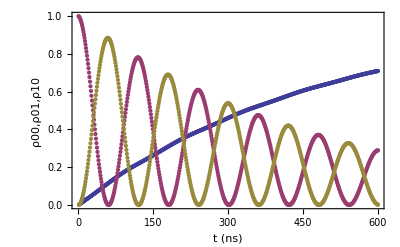

```mathematica
ta1=Table[ρVec2Prim[t],{t,0,600}];
ρ00List1=#[[1,1]]&/@ta1;
ρ01List1=#[[2,2]]&/@ta1;
ρ10List1=#[[3,3]]&/@ta1;
gr1=ListPlot[{ρ00List1,ρ01List1,ρ10List1},Frame->True,FrameLabel->{"t (ns)","ρ00,ρ01,ρ10"}]
ρGraphList0=complexMatrixDraw[#1,myOpts1]&/@ta1;
```

```mathematica
(*ListAnimate[ρGraphList0]*)
```

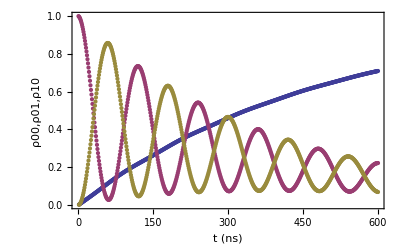

```mathematica
ta1c=Table[ρVec2Primc[t],{t,0,600}];
ρ00List1c=#[[1,1]]&/@ta1c;
ρ01List1c=#[[2,2]]&/@ta1c;
ρ10List1c=#[[3,3]]&/@ta1c;
gr1c=ListPlot[{ρ00List1c,ρ01List1c,ρ10List1c},Frame->True,FrameLabel->{"t (ns)","ρ00,ρ01,ρ10"}]
ρGraphList0c=complexMatrixDraw[#1,myOpts1]&/@ta1c;
```

```mathematica
ρGraphList0c[[1]]
```

-Graphics-

```mathematica
(*ListAnimate[ρGraphList0c]*)
```

$Aborted[]

## Import, analyse, and treat data

Directory : [Lab computer]\Labo\local - expdata\FO - C5 \3rd - Run \2011_ 02 _ 09\film of swapPauli Set : State Tomography of Swap vs Swap Duration_Quantum Process Tomography at time 26 - 0 _ 0 _Swap of state 0 _ 0 _ 180 _ 0 - 0 _ 0 _Measured spins - 300 _ 0. txt
Density Matrices : State Tomography of Swap vs Swap Duration_Quantum Process Tomography at time 26 - 0 _ 0 _Swap of state 0 _ 0 _ 180 _ 0 - 0 _ 0 _Measured spins - 300 _ 0 _Density Matrices - 300 _ 0. txt

### define the operators and showPauliSet function

```mathematica
opBase1NameA={"i","x","y","z"};
Clear[id,σx,σy,σz,iσy];
opBase1A={id,σx,σy,σz};
opBase2NameA=Outer[StringJoin,opBase1NameA,opBase1NameA]//Flatten
opBase2A=Outer[KroneckerProduct,opBase1A,opBase1A]//Flatten;
id={{1,0},{0,1}};
σx={{0,1},{1,0}};
σy={{0,-ⅈ},{ⅈ,0}};
iσy=I σy;
σz={{1,0},{0,-1}};
opBase1A=opBase1A;
opBase2A=opBase2A;
MatrixForm/@opBase2A
```

{ii,ix,iy,iz,xi,xx,xy,xz,yi,yx,yy,yz,zi,zx,zy,zz}

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)}

```mathematica
ticks={Transpose[{Range[16],ToUpperCase/@opBase2NameA}],{-1,-0.5,0,0.5,1}};
showPauliSet[pauliSetlist_,opts___]:=ListPlot[pauliSetlist,Frame->True,PlotStyle->{{Red,PointSize[Large]},{Blue,PointSize[Medium]},{RGBColor[0,0.5,0]},{Magenta}},PlotRange->{{0.5,16.5},{-1.05,1.05}},FrameTicks->ticks,opts]
```

### import pauli sets

We import the measured Pauli sets (readout errors corrected) and reorder each Pauli set according to the opBase2Names order

```mathematica
pauliSets=Import["L:\\local-expdata\\FO-C5\\3rd-Run\\2011_02_09\\film of swap\\State Tomography of Swap vs Swap Duration_Quantum Process Tomography at time 26-0_0_Swap of state 0_0_180_0-0_0_Measured spins-300_0.txt","Table"];
pauliSets[[1]]
set=Rest[pauliSets[[1]]]
orderOp=Position[set,#]&/@opBase2NameA//Flatten
times=Rest[Transpose[pauliSets][[1]]]
pauliSets=Rest[pauliSets];
pauliSets=(Rest[#]&/@pauliSets);
reorderPauliSet[ps_]:=ps[[#]]&/@orderOp;
pauliSets=reorderPauliSet/@pauliSets;
Dimensions[pauliSets]
opBase2NameA
```

{t,xx,xy,xz,xi,yx,yy,yz,yi,zx,zy,zz,zi,ix,iy,iz,ii}

{xx,xy,xz,xi,yx,yy,yz,yi,zx,zy,zz,zi,ix,iy,iz,ii}

{16,13,14,15,4,1,2,3,8,5,6,7,12,9,10,11}

{0.,2.,4.,6.,8.,10.,12.,14.,16.,18.,20.,22.,24.,26.,28.,30.,32.,34.,36.,38.,40.,42.,44.,46.,48.,50.,52.,54.,56.,58.,60.,62.,64.,66.,68.,70.,72.,74.,76.,78.,80.,82.,84.,86.,88.,90.,92.,94.,96.,98.,100.,102.,104.,106.,108.,110.,112.,114.,116.,118.,120.,122.,124.,126.,128.,130.,132.,134.,136.,138.,140.,142.,144.,146.,148.,150.,152.,154.,156.,158.,160.,162.,164.,166.,168.,170.,172.,174.,176.,178.,180.,182.,184.,186.,188.,190.,192.,194.,196.,198.,200.,202.,204.,206.,208.,210.,212.,214.,216.,218.,220.,222.,224.,226.,228.,230.,232.,234.,236.,238.,240.,242.,244.,246.,248.,250.,252.,254.,256.,258.,260.,262.,264.,266.,268.,270.,272.,274.,276.,278.,280.,282.,284.,286.,288.,290.,292.,294.,296.,298.,300.,302.,304.,306.,308.,310.,312.,314.,316.,318.,320.,322.,324.,326.,328.,330.,332.,334.,336.,338.,340.,342.,344.,346.,348.,350.,352.,354.,356.,358.,360.,362.,364.,366.,368.,370.,372.,374.,376.,378.,380.,382.,384.,386.,388.,390.,392.,394.,396.,398.,400.,402.,404.,406.,408.,410.,412.,414.,416.,418.,420.,422.,424.,426.,428.,430.,432.,434.,436.,438.,440.,442.,444.,446.,448.,450.,452.,454.,456.,458.,460.,462.,464.,466.,468.,470.,472.,474.,476.,478.,480.,482.,484.,486.,488.,490.,492.,494.,496.,498.,500.,502.,504.,506.,508.,510.,512.,514.,516.,518.,520.,522.,524.,526.,528.,530.,532.,534.,536.,538.,540.,542.,544.,546.,548.,550.,552.,554.,556.,558.,560.,562.,564.,566.,568.,570.,572.,574.,576.,578.,580.,582.,584.,586.,588.,590.,592.,594.,596.,598.}

{300,16}

{ii,ix,iy,iz,xi,xx,xy,xz,yi,yx,yy,yz,zi,zx,zy,zz}

Let's plot them.

```mathematica
pauliGraphList=MapThread[showPauliSet[{#1},PlotLabel->"t="<>ToString[#2]<>"ns"]&,{pauliSets,times}];
ListAnimate[pauliGraphList]
```

### from Pauli sets to density matrices and vice and versa

Now we calculate the expectation values of the Pauli operators < Pi > = Tr(ρ.Pi) as a function of ρ: {<Pi>}=A.ρ

```mathematica
ρM1={{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}};
(ρV1=Transpose[ρM1]//Flatten)//MatrixForm
(meanValues=Tr[ρM1.#]&/@opBase2A)//MatrixForm
(matA=CoefficientArrays[meanValues,ρV1]//Normal//#[[2]]&)//MatrixForm
pauliSetFromρ=matA.Flatten[Transpose[#]]&;
(matAInv=Inverse[matA])//MatrixForm
```

(ρ11
ρ21
ρ31
ρ41
ρ12
ρ22
ρ32
ρ42
ρ13
ρ23
ρ33
ρ43
ρ14
ρ24
ρ34
ρ44)

(ρ11+ρ22+ρ33+ρ44
ρ12+ρ21+ρ34+ρ43
ⅈ ρ12-ⅈ ρ21+ⅈ ρ34-ⅈ ρ43
ρ11-ρ22+ρ33-ρ44
ρ13+ρ24+ρ31+ρ42
ρ14+ρ23+ρ32+ρ41
ⅈ ρ14-ⅈ ρ23+ⅈ ρ32-ⅈ ρ41
ρ13-ρ24+ρ31-ρ42
ⅈ ρ13+ⅈ ρ24-ⅈ ρ31-ⅈ ρ42
ⅈ ρ14+ⅈ ρ23-ⅈ ρ32-ⅈ ρ41
-ρ14+ρ23+ρ32-ρ41
ⅈ ρ13-ⅈ ρ24-ⅈ ρ31+ⅈ ρ42
ρ11+ρ22-ρ33-ρ44
ρ12+ρ21-ρ34-ρ43
ⅈ ρ12-ⅈ ρ21-ⅈ ρ34+ⅈ ρ43
ρ11-ρ22-ρ33+ρ44)

(1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0
1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | ⅈ | ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0
0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0
1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1)

(1/4 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 1/4
0 | 1/4 | ⅈ/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | ⅈ/4 | 0
0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 1/4 | ⅈ/4 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/4 | ⅈ/4 | 0 | 0 | ⅈ/4 | -1/4 | 0 | 0 | 0 | 0 | 0
0 | 1/4 | -ⅈ/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | -ⅈ/4 | 0
1/4 | 0 | 0 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | -1/4
0 | 0 | 0 | 0 | 0 | 1/4 | -ⅈ/4 | 0 | 0 | ⅈ/4 | 1/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/4 | 0 | 0 | -1/4 | ⅈ/4 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 1/4 | -ⅈ/4 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/4 | ⅈ/4 | 0 | 0 | -ⅈ/4 | 1/4 | 0 | 0 | 0 | 0 | 0
1/4 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 | 0 | 0 | -1/4
0 | 1/4 | ⅈ/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 | -ⅈ/4 | 0
0 | 0 | 0 | 0 | 0 | 1/4 | -ⅈ/4 | 0 | 0 | -ⅈ/4 | -1/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/4 | 0 | 0 | -1/4 | -ⅈ/4 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0
0 | 1/4 | -ⅈ/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 | ⅈ/4 | 0
1/4 | 0 | 0 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 | 0 | 0 | 1/4)

Finally we calculate the density matrices ρ by linear inversion  ρ = A^-1{<Pi>}...

```mathematica
ρFromPauliSet=Chop[Transpose[Partition[matAInv.#,4]]]&;
ρs=ρFromPauliSet/@pauliSets;
ρs//Dimensions
```

{300,4,4}

```mathematica
ρGraphList=myCompareGraph[{#1}]&/@ρs;
ListAnimate[ρGraphList]
```

### analysis of the systematic preparation and tomographic pulse errors

#### Introducing the problem

```mathematica
ticks={Transpose[{Range[16],ToUpperCase/@opBase2NameA}],{-1,-0.5,0,0.5,1}};
showPauliSet[pauliSetlist_]:=ListPlot[pauliSetlist,Frame->True,PlotStyle->{{Red,PointSize[Large]},{Blue,PointSize[Medium]},{RGBColor[0,0.5,0]}},PlotRange->{{0.5,16.5},{-1.05,1.05}},FrameTicks->ticks]
```

Despite fidelities close to 1, we notice large spurious matrix elements in the input ρ's. So we suspect large pulse errors, which we try to determine.

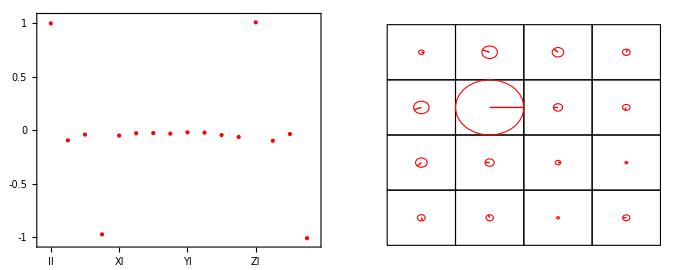

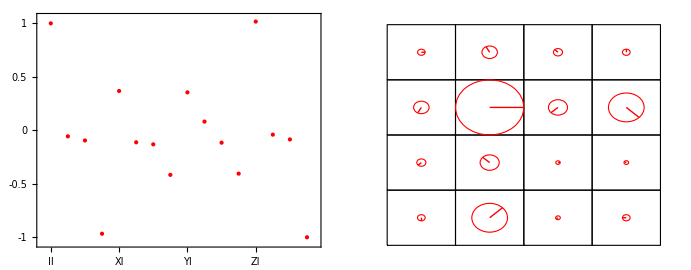

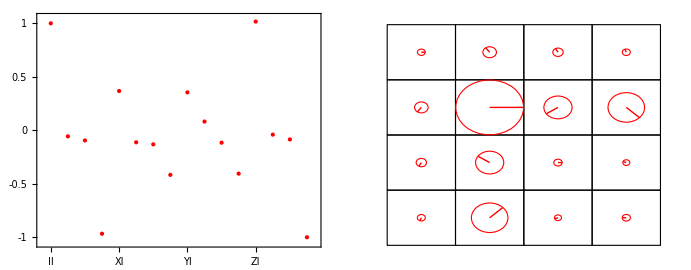

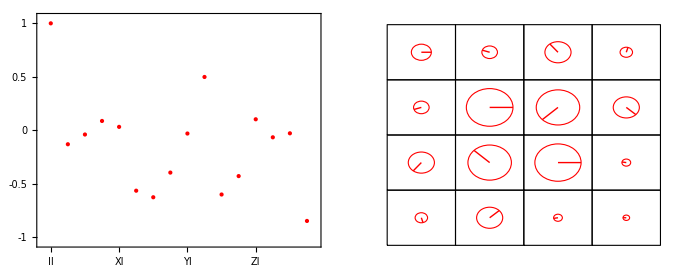

```mathematica
GraphicsRow[{showPauliSet[pauliSets[[1]]],myCompareGraph[{ρs[[1]]}]}]
GraphicsRow[{showPauliSet[pauliSets[[2]]],myCompareGraph[{ρs[[2]]}]}]
GraphicsRow[{showPauliSet[pauliSets[[2]]],myCompareGraph[{ρs[[3]]}]}]
GraphicsRow[{showPauliSet[pauliSets[[16]]],myCompareGraph[{ρs[[16]]}]}]
```

#### A few plots

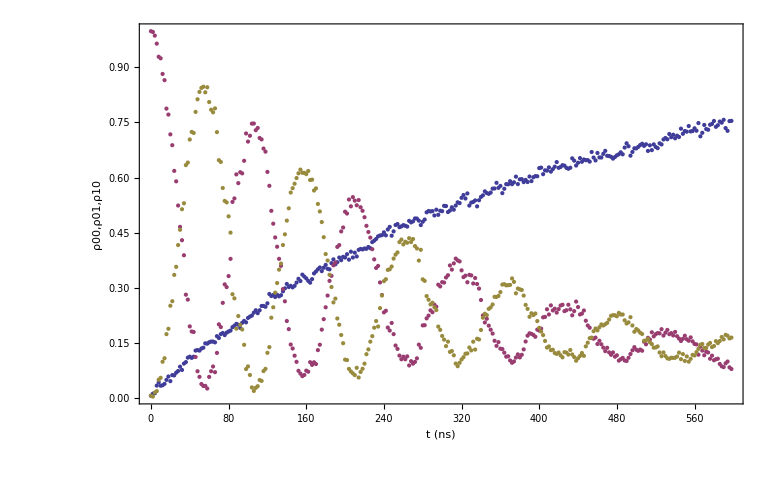

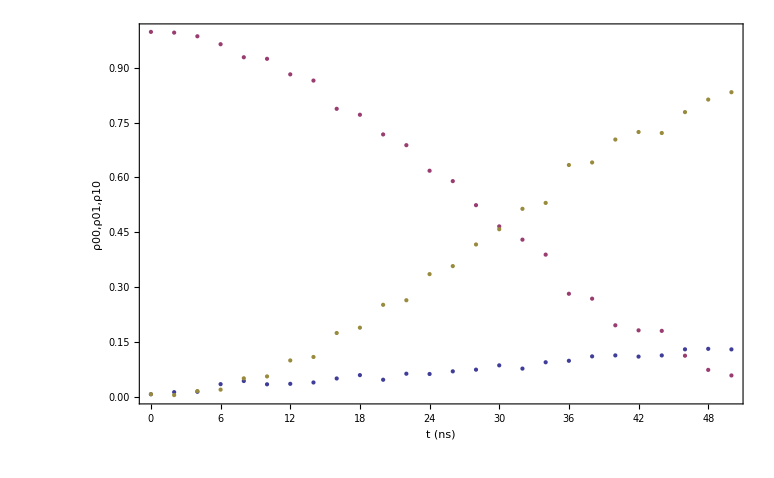

```mathematica
ρ00List=Transpose[{times,#[[1,1]]&/@ρs}];
ρ01List=Transpose[{times,#[[2,2]]&/@ρs}];
ρ10List=Transpose[{times,#[[3,3]]&/@ρs}];
gr0=ListPlot[{ρ00List,ρ01List,ρ10List},Frame->True,FrameLabel->{"t (ns)","ρ00,ρ01,ρ10"}]
Show[%,PlotRange->{{0,50},{0,1}}]
```

```mathematica
extrema={0,0.02843,0.05491,0.0806,0.106}*2;
derivative=(RotateLeft[extrema]-extrema)//Most
speed=1/derivative derivative[[1]] 8.6
time=(RotateLeft[extrema]+extrema)/2//Most
```

{0.05686,0.05296,0.05138,0.0508}

{8.6,9.23331,9.51724,9.62591}

{0.02843,0.08334,0.13551,0.1866}

```mathematica
ts={time,speed}//Transpose
```

{{0.02843,8.6},{0.08334,9.23331},{0.13551,9.51724},{0.1866,9.62591}}

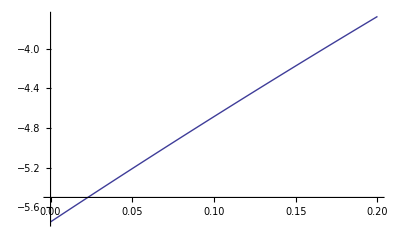

```mathematica
Plot[8(2-Exp[-t/2+1]),{t,0,0.2}]
```

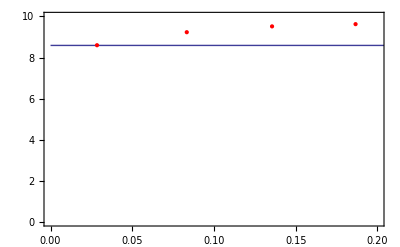

```mathematica
Show[ListPlot[ts,Frame->True,Axes->False,PlotStyle->{Red,PointSize[Large]},PlotRange->{{0,0.2},{0,10}}],Plot[{8.59},{t,0,2}]]
```

Sur une demi periode, la vitesse augmente dun rapport

```mathematica
378/351.
```

1.07692

ce qui correspond à un detuning de 1/2(Δ/ωSwap)^2=8% soit Δ/ωSwap=

```mathematica
Sqrt[2*.077]
```

0.392428

C'est énorme, mais le detuning est faible entre 0 et le iSWAP, ce qui permet décarter le detuning du modèle d'erreur.

```mathematica
0.05 8.6
```

0.43

avec detuning

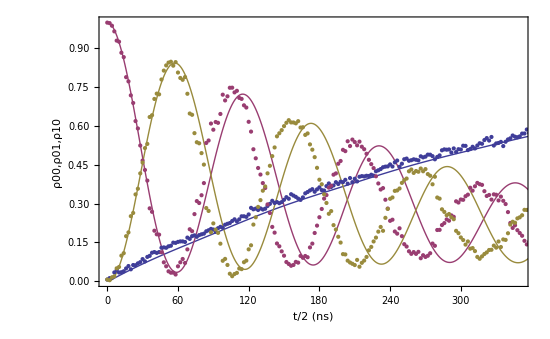

```mathematica
λP0d=λProcess[{2π 0.0086,2π.0086 *0.1,0,0,0,0,2π 0.122 t,0,.040 2π.0086,.045 2π.0086,.02 2π.0086,.02 2π.0086,t}]//Chop;
(ρVec2d=ρVecFromρ[ρListIn[[2]]])//MatrixForm;
ρFromρVec[ρVec2d]//MatrixForm;
ρVec2Primd[t_]=ρFromρVec[λP0d.ρVec2d];
tad=Table[ρVec2Primd[t],{t,0,600}];
ρ00List1d=#[[1,1]]&/@tad;
ρ01List1d=#[[2,2]]&/@tad;
ρ10List1d=#[[3,3]]&/@tad;
gr1d=ListPlot[{ρ00List1d,ρ01List1d,ρ10List1d},Frame->True,FrameLabel->{"t/2 (ns)","ρ00,ρ01,ρ10"},Joined->True];
Show[gr1d,gr0,PlotRange->{{0,350},{0,1}}]
```

```mathematica
ρGraphList0d=complexMatrixDraw[#1,myOpts1]&/@tad;
ListAnimate[ρGraphList0d]
```

$Aborted[]

#### Error model

```mathematica
opBase2NameA
```

{ii,ix,iy,iz,xi,xx,xy,xz,yi,yx,yy,yz,zi,zx,zy,zz}

We assume the following systematic errors:  
	- " π rotation" around of  π+ϵπx  with different ϵπx for qubit 1 and 2;
	- " π/2 rotation" of  π/2 + ϵhπ with different ϵhπ for qubit 1 and 2  and for x and y axis ;
	- y axis making 90°+ θy with x axis, with different θy for qubit 1 and 2;
	- x-y frame at tomography rotated by θt with respect to x-y frame at preparation,  with different θt for qubit 1 and 2.
As a consequence :	
	- instead of preparing the states |01>, we prepaare another  state
	-instead of measuring the expectation values of  opBase1, we measure those of opBase1E with errors

Instead of preparing   |01>, we actually prepare a state ρ0In.
We check that ρ0InE=|01><01|=ρListIn[[2]] when all errors are zeroed.

```mathematica
Clear[ρInE]
```

```mathematica
Clear[id,rx2]
opE=KroneckerProduct[id,rx2[π]];
id={{1,0},{0,1}};
rx2[π]=MatrixExp[- I (π+ϵπx2Prep)/2 σx];
(opE=opE)//MatrixForm;
noErrorRule={ϵπx2Prep->0};
(ρInE[ϵπx2Prep_]=opE.ρListIn[[1]].ConjugateTranspose[opE]//FullSimplify[#,Assumptions->{ϵπx2Prep ∈Reals}]&)//MatrixForm
(ρInNoE=ρInE[0])//MatrixForm
ρInNoE==ρListIn[[2]]
```

(Sin[ϵπx2Prep/2]^2 | -1/2 ⅈ Sin[ϵπx2Prep] | 0 | 0
1/2 ⅈ Sin[ϵπx2Prep] | Cos[ϵπx2Prep/2]^2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

True

- instead of measuring i,x,y,z, we measure i,xp,yp,z with up=Rudagger Z Ru and Ru the rotation (with errors) trying to bring u along z.
The list of  measured operators is opE2b instead of opBase2.

```mathematica
Clear[id,xe1,ye1,xe2,ye2,σz,iye1,iye2];
opE1b1={id,xe1,ye1,σz};
opE1b2={id,xe2,ye2,σz};
opE2b=Outer[KroneckerProduct,opE1b1,opE1b2]//Flatten;
opE1b1I={id,xe1,iye1,σz};
opE1b2I={id,xe2,iye2,σz};
opE2bI=Outer[KroneckerProduct,opE1b1I,opE1b2I]//Flatten;
id={{1,0},{0,1}};
σx={{0,1},{1,0}};
σy={{0,-ⅈ},{ⅈ,0}};
iσy=I σy;
σz={{1,0},{0,-1}};
rx1[π/2]=MatrixExp[ -I (π/2+ϵhπx1Tomo)/2 (Cos[θt1]σx+Sin[θt1]σy)];
rx2[π/2]=MatrixExp[- I (π/2+ϵhπx2Tomo)/2(Cos[θt2]σx+Sin[θt2]σy)];
ry1[-π/2]=MatrixExp[ I (π/2+ϵhπy1Tomo)/2 (Cos[θy1+θt1]σy-Sin[θy1+θt1]σx)];
ry2[-π/2]=MatrixExp[I (π/2+ϵhπy2Tomo)/2 (Cos[θy2+θt2]σy-Sin[θy2+θt2]σx)];
xe1=ConjugateTranspose[ry1[-π/2]].σz.ry1[-π/2]//ComplexExpand//Simplify;
ye1= ConjugateTranspose[rx1[π/2]].σz.rx1[π/2]//ComplexExpand//Simplify;
xe2=ConjugateTranspose[ry2[-π/2]].σz.ry2[-π/2]//ComplexExpand//Simplify;
ye2= ConjugateTranspose[rx2[π/2]].σz.rx2[π/2]//ComplexExpand//Simplify;
iye1=I ye1;
iye2=I ye2;
opE2b=opE2b//FullSimplify;
opE2bI=opE2bI//FullSimplify;
noErrorRule=noErrorRule~Join~{ϵhπx1Tomo->0,ϵhπx2Tomo->0,ϵhπy1Tomo->0,ϵhπy2Tomo->0,θy1->0,θy2->0,θt1->0,θt2->0};
opE2b=opE2b//FullSimplify;
opE2bI=opE2bI//FullSimplify;
opNoEI=opE2bI/.noErrorRule;
(opNoEI-opBase2//Flatten//Max)==0
Print ["opE2b="]
MatrixForm/@opE2b
```

True

opE2b=

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] (Cos[θt2+θy2]-ⅈ Sin[θt2+θy2]) | 0 | 0
Cos[ϵhπy2Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Sin[ϵhπy2Tomo] | 0 | 0
0 | 0 | -Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] (Cos[θt2+θy2]-ⅈ Sin[θt2+θy2])
0 | 0 | Cos[ϵhπy2Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Sin[ϵhπy2Tomo]),(-Sin[ϵhπx2Tomo] | Cos[ϵhπx2Tomo] (-ⅈ Cos[θt2]-Sin[θt2]) | 0 | 0
ⅈ ⅇ^(ⅈ θt2) Cos[ϵhπx2Tomo] | Sin[ϵhπx2Tomo] | 0 | 0
0 | 0 | -Sin[ϵhπx2Tomo] | Cos[ϵhπx2Tomo] (-ⅈ Cos[θt2]-Sin[θt2])
0 | 0 | ⅈ ⅇ^(ⅈ θt2) Cos[ϵhπx2Tomo] | Sin[ϵhπx2Tomo]),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(-Sin[ϵhπy1Tomo] | 0 | Cos[ϵhπy1Tomo] (Cos[θt1+θy1]-ⅈ Sin[θt1+θy1]) | 0
0 | -Sin[ϵhπy1Tomo] | 0 | Cos[ϵhπy1Tomo] (Cos[θt1+θy1]-ⅈ Sin[θt1+θy1])
Cos[ϵhπy1Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | 0 | Sin[ϵhπy1Tomo] | 0
0 | Cos[ϵhπy1Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | 0 | Sin[ϵhπy1Tomo]),(Sin[ϵhπy1Tomo] Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] Sin[ϵhπy1Tomo] (-Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Cos[ϵhπy1Tomo] Sin[ϵhπy2Tomo] (-Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | Cos[ϵhπy1Tomo] Cos[ϵhπy2Tomo] (Cos[θt1+θt2+θy1+θy2]-ⅈ Sin[θt1+θt2+θy1+θy2])
-Cos[ϵhπy2Tomo] Sin[ϵhπy1Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | -Sin[ϵhπy1Tomo] Sin[ϵhπy2Tomo] | Cos[ϵhπy1Tomo] Cos[ϵhπy2Tomo] (Cos[θt1+θy1]-ⅈ Sin[θt1+θy1]) (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Cos[ϵhπy1Tomo] Sin[ϵhπy2Tomo] (Cos[θt1+θy1]-ⅈ Sin[θt1+θy1])
-Cos[ϵhπy1Tomo] Sin[ϵhπy2Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | Cos[ϵhπy1Tomo] Cos[ϵhπy2Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) (Cos[θt2+θy2]-ⅈ Sin[θt2+θy2]) | -Sin[ϵhπy1Tomo] Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] Sin[ϵhπy1Tomo] (Cos[θt2+θy2]-ⅈ Sin[θt2+θy2])
Cos[ϵhπy1Tomo] Cos[ϵhπy2Tomo] (Cos[θt1+θt2+θy1+θy2]+ⅈ Sin[θt1+θt2+θy1+θy2]) | Cos[ϵhπy1Tomo] Sin[ϵhπy2Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | Cos[ϵhπy2Tomo] Sin[ϵhπy1Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Sin[ϵhπy1Tomo] Sin[ϵhπy2Tomo]),(Sin[ϵhπx2Tomo] Sin[ϵhπy1Tomo] | Cos[ϵhπx2Tomo] Sin[ϵhπy1Tomo] (ⅈ Cos[θt2]+Sin[θt2]) | Cos[ϵhπy1Tomo] Sin[ϵhπx2Tomo] (-Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | Cos[ϵhπx2Tomo] Cos[ϵhπy1Tomo] (-ⅈ Cos[θt1+θt2+θy1]-Sin[θt1+θt2+θy1])
Cos[ϵhπx2Tomo] Sin[ϵhπy1Tomo] (-ⅈ Cos[θt2]+Sin[θt2]) | -Sin[ϵhπx2Tomo] Sin[ϵhπy1Tomo] | Cos[ϵhπx2Tomo] Cos[ϵhπy1Tomo] (ⅈ Cos[θt1-θt2+θy1]+Sin[θt1-θt2+θy1]) | Cos[ϵhπy1Tomo] Sin[ϵhπx2Tomo] (Cos[θt1+θy1]-ⅈ Sin[θt1+θy1])
-Cos[ϵhπy1Tomo] Sin[ϵhπx2Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | Cos[ϵhπx2Tomo] Cos[ϵhπy1Tomo] (-ⅈ Cos[θt1-θt2+θy1]+Sin[θt1-θt2+θy1]) | -Sin[ϵhπx2Tomo] Sin[ϵhπy1Tomo] | Cos[ϵhπx2Tomo] Sin[ϵhπy1Tomo] (-ⅈ Cos[θt2]-Sin[θt2])
Cos[ϵhπx2Tomo] Cos[ϵhπy1Tomo] (ⅈ Cos[θt1+θt2+θy1]-Sin[θt1+θt2+θy1]) | Cos[ϵhπy1Tomo] Sin[ϵhπx2Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | ⅈ ⅇ^(ⅈ θt2) Cos[ϵhπx2Tomo] Sin[ϵhπy1Tomo] | Sin[ϵhπx2Tomo] Sin[ϵhπy1Tomo]),(-Sin[ϵhπy1Tomo] | 0 | Cos[ϵhπy1Tomo] (Cos[θt1+θy1]-ⅈ Sin[θt1+θy1]) | 0
0 | Sin[ϵhπy1Tomo] | 0 | Cos[ϵhπy1Tomo] (-Cos[θt1+θy1]+ⅈ Sin[θt1+θy1])
Cos[ϵhπy1Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | 0 | Sin[ϵhπy1Tomo] | 0
0 | -Cos[ϵhπy1Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | 0 | -Sin[ϵhπy1Tomo]),(-Sin[ϵhπx1Tomo] | 0 | Cos[ϵhπx1Tomo] (-ⅈ Cos[θt1]-Sin[θt1]) | 0
0 | -Sin[ϵhπx1Tomo] | 0 | Cos[ϵhπx1Tomo] (-ⅈ Cos[θt1]-Sin[θt1])
ⅈ ⅇ^(ⅈ θt1) Cos[ϵhπx1Tomo] | 0 | Sin[ϵhπx1Tomo] | 0
0 | ⅈ ⅇ^(ⅈ θt1) Cos[ϵhπx1Tomo] | 0 | Sin[ϵhπx1Tomo]),(Sin[ϵhπx1Tomo] Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] Sin[ϵhπx1Tomo] (-Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Cos[ϵhπx1Tomo] Sin[ϵhπy2Tomo] (ⅈ Cos[θt1]+Sin[θt1]) | Cos[ϵhπx1Tomo] Cos[ϵhπy2Tomo] (-ⅈ Cos[θt1+θt2+θy2]-Sin[θt1+θt2+θy2])
-Cos[ϵhπy2Tomo] Sin[ϵhπx1Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | -Sin[ϵhπx1Tomo] Sin[ϵhπy2Tomo] | ⅇ^(-ⅈ θt1) Cos[ϵhπx1Tomo] Cos[ϵhπy2Tomo] (-ⅈ Cos[θt2+θy2]+Sin[θt2+θy2]) | Cos[ϵhπx1Tomo] Sin[ϵhπy2Tomo] (-ⅈ Cos[θt1]-Sin[θt1])
Cos[ϵhπx1Tomo] Sin[ϵhπy2Tomo] (-ⅈ Cos[θt1]+Sin[θt1]) | ⅇ^(ⅈ θt1) Cos[ϵhπx1Tomo] Cos[ϵhπy2Tomo] (ⅈ Cos[θt2+θy2]+Sin[θt2+θy2]) | -Sin[ϵhπx1Tomo] Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] Sin[ϵhπx1Tomo] (Cos[θt2+θy2]-ⅈ Sin[θt2+θy2])
Cos[ϵhπx1Tomo] Cos[ϵhπy2Tomo] (ⅈ Cos[θt1+θt2+θy2]-Sin[θt1+θt2+θy2]) | ⅈ ⅇ^(ⅈ θt1) Cos[ϵhπx1Tomo] Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] Sin[ϵhπx1Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Sin[ϵhπx1Tomo] Sin[ϵhπy2Tomo]),(Sin[ϵhπx1Tomo] Sin[ϵhπx2Tomo] | Cos[ϵhπx2Tomo] Sin[ϵhπx1Tomo] (ⅈ Cos[θt2]+Sin[θt2]) | Cos[ϵhπx1Tomo] Sin[ϵhπx2Tomo] (ⅈ Cos[θt1]+Sin[θt1]) | Cos[ϵhπx1Tomo] Cos[ϵhπx2Tomo] (-Cos[θt1+θt2]+ⅈ Sin[θt1+θt2])
Cos[ϵhπx2Tomo] Sin[ϵhπx1Tomo] (-ⅈ Cos[θt2]+Sin[θt2]) | -Sin[ϵhπx1Tomo] Sin[ϵhπx2Tomo] | ⅇ^(-ⅈ (θt1-θt2)) Cos[ϵhπx1Tomo] Cos[ϵhπx2Tomo] | Cos[ϵhπx1Tomo] Sin[ϵhπx2Tomo] (-ⅈ Cos[θt1]-Sin[θt1])
Cos[ϵhπx1Tomo] Sin[ϵhπx2Tomo] (-ⅈ Cos[θt1]+Sin[θt1]) | ⅇ^(ⅈ (θt1-θt2)) Cos[ϵhπx1Tomo] Cos[ϵhπx2Tomo] | -Sin[ϵhπx1Tomo] Sin[ϵhπx2Tomo] | Cos[ϵhπx2Tomo] Sin[ϵhπx1Tomo] (-ⅈ Cos[θt2]-Sin[θt2])
-Cos[ϵhπx1Tomo] Cos[ϵhπx2Tomo] (Cos[θt1+θt2]+ⅈ Sin[θt1+θt2]) | ⅈ ⅇ^(ⅈ θt1) Cos[ϵhπx1Tomo] Sin[ϵhπx2Tomo] | ⅈ ⅇ^(ⅈ θt2) Cos[ϵhπx2Tomo] Sin[ϵhπx1Tomo] | Sin[ϵhπx1Tomo] Sin[ϵhπx2Tomo]),(-Sin[ϵhπx1Tomo] | 0 | Cos[ϵhπx1Tomo] (-ⅈ Cos[θt1]-Sin[θt1]) | 0
0 | Sin[ϵhπx1Tomo] | 0 | Cos[ϵhπx1Tomo] (ⅈ Cos[θt1]+Sin[θt1])
ⅈ ⅇ^(ⅈ θt1) Cos[ϵhπx1Tomo] | 0 | Sin[ϵhπx1Tomo] | 0
0 | Cos[ϵhπx1Tomo] (-ⅈ Cos[θt1]+Sin[θt1]) | 0 | -Sin[ϵhπx1Tomo]),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] (Cos[θt2+θy2]-ⅈ Sin[θt2+θy2]) | 0 | 0
Cos[ϵhπy2Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Sin[ϵhπy2Tomo] | 0 | 0
0 | 0 | Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] (-Cos[θt2+θy2]+ⅈ Sin[θt2+θy2])
0 | 0 | -Cos[ϵhπy2Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | -Sin[ϵhπy2Tomo]),(-Sin[ϵhπx2Tomo] | Cos[ϵhπx2Tomo] (-ⅈ Cos[θt2]-Sin[θt2]) | 0 | 0
ⅈ ⅇ^(ⅈ θt2) Cos[ϵhπx2Tomo] | Sin[ϵhπx2Tomo] | 0 | 0
0 | 0 | Sin[ϵhπx2Tomo] | Cos[ϵhπx2Tomo] (ⅈ Cos[θt2]+Sin[θt2])
0 | 0 | Cos[ϵhπx2Tomo] (-ⅈ Cos[θt2]+Sin[θt2]) | -Sin[ϵhπx2Tomo]),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)}

#### Pauli sets with error and apparent density matrices

The measured Pauli sets {Tr[ρE.PauliE]} contain both preparation and tomography pulse errors

```mathematica
params={ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,θt1,θt2};
params0=ConstantArray[0,Length[params]];
paramRule[paramsNum_]:=MapThread[#1->#2&,{params,paramsNum}]
```

```mathematica
pauliSetError[paramsNum_,ρMi_]:=Tr[ρMi.#]&/@(opE2b/.MapThread[#1->#2&,{params,paramsNum}])
pauliSetInE[{ϵπx2Prep_,ϵhπx1Tomo_,ϵhπx2Tomo_,ϵhπy1Tomo_,ϵhπy2Tomo_,θy1_,θy2_,θt1_,θt2_}]=pauliSetError[params,ρInE[ϵπx2Prep]]//FullSimplify[#,Assumptions->(#∈Reals&/@params)]&
(ρInA[{ϵπx2Prep_,ϵhπx1Tomo_,ϵhπx2Tomo_,ϵhπy1Tomo_,ϵhπy2Tomo_,θy1_,θy2_,θt1_,θt2_}]=ρFromPauliSet[pauliSetInE[{ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,θt1,θt2}]]//FullSimplify)//MatrixForm
pauliSetInE[params0]
ρInA[params0]//MatrixForm
```

{1,Cos[ϵπx2Prep] Sin[ϵhπy2Tomo]+Cos[ϵhπy2Tomo] Sin[ϵπx2Prep] Sin[θt2+θy2],Cos[ϵπx2Prep] Sin[ϵhπx2Tomo]+Cos[ϵhπx2Tomo] Cos[θt2] Sin[ϵπx2Prep],-Cos[ϵπx2Prep],-Sin[ϵhπy1Tomo],-Sin[ϵhπy1Tomo] (Cos[ϵπx2Prep] Sin[ϵhπy2Tomo]+Cos[ϵhπy2Tomo] Sin[ϵπx2Prep] Sin[θt2+θy2]),-Sin[ϵhπy1Tomo] (Cos[ϵπx2Prep] Sin[ϵhπx2Tomo]+Cos[ϵhπx2Tomo] Cos[θt2] Sin[ϵπx2Prep]),Cos[ϵπx2Prep] Sin[ϵhπy1Tomo],-Sin[ϵhπx1Tomo],-Sin[ϵhπx1Tomo] (Cos[ϵπx2Prep] Sin[ϵhπy2Tomo]+Cos[ϵhπy2Tomo] Sin[ϵπx2Prep] Sin[θt2+θy2]),-Sin[ϵhπx1Tomo] (Cos[ϵπx2Prep] Sin[ϵhπx2Tomo]+Cos[ϵhπx2Tomo] Cos[θt2] Sin[ϵπx2Prep]),Cos[ϵπx2Prep] Sin[ϵhπx1Tomo],1,Cos[ϵπx2Prep] Sin[ϵhπy2Tomo]+Cos[ϵhπy2Tomo] Sin[ϵπx2Prep] Sin[θt2+θy2],Cos[ϵπx2Prep] Sin[ϵhπx2Tomo]+Cos[ϵhπx2Tomo] Cos[θt2] Sin[ϵπx2Prep],-Cos[ϵπx2Prep]}

(Sin[ϵπx2Prep/2]^2 | 1/2 (Cos[ϵπx2Prep] (-ⅈ Sin[ϵhπx2Tomo]+Sin[ϵhπy2Tomo])+Sin[ϵπx2Prep] (-ⅈ Cos[ϵhπx2Tomo] Cos[θt2]+Cos[ϵhπy2Tomo] Sin[θt2+θy2])) | 1/4 (-1+Cos[ϵπx2Prep]) (-ⅈ Sin[ϵhπx1Tomo]+Sin[ϵhπy1Tomo]) | 1/4 (Sin[ϵhπx1Tomo]+ⅈ Sin[ϵhπy1Tomo]) (Cos[ϵπx2Prep] (Sin[ϵhπx2Tomo]+ⅈ Sin[ϵhπy2Tomo])+Sin[ϵπx2Prep] (Cos[ϵhπx2Tomo] Cos[θt2]+ⅈ Cos[ϵhπy2Tomo] Sin[θt2+θy2]))
1/2 (Cos[ϵπx2Prep] (ⅈ Sin[ϵhπx2Tomo]+Sin[ϵhπy2Tomo])+Sin[ϵπx2Prep] (ⅈ Cos[ϵhπx2Tomo] Cos[θt2]+Cos[ϵhπy2Tomo] Sin[θt2+θy2])) | Cos[ϵπx2Prep/2]^2 | -1/4 (Sin[ϵhπx1Tomo]+ⅈ Sin[ϵhπy1Tomo]) (Cos[ϵπx2Prep] (Sin[ϵhπx2Tomo]-ⅈ Sin[ϵhπy2Tomo])+Sin[ϵπx2Prep] (Cos[ϵhπx2Tomo] Cos[θt2]-ⅈ Cos[ϵhπy2Tomo] Sin[θt2+θy2])) | 1/2 ⅈ Cos[ϵπx2Prep/2]^2 (Sin[ϵhπx1Tomo]+ⅈ Sin[ϵhπy1Tomo])
1/4 (-1+Cos[ϵπx2Prep]) (ⅈ Sin[ϵhπx1Tomo]+Sin[ϵhπy1Tomo]) | -1/4 (Sin[ϵhπx1Tomo]-ⅈ Sin[ϵhπy1Tomo]) (Cos[ϵπx2Prep] (Sin[ϵhπx2Tomo]+ⅈ Sin[ϵhπy2Tomo])+Sin[ϵπx2Prep] (Cos[ϵhπx2Tomo] Cos[θt2]+ⅈ Cos[ϵhπy2Tomo] Sin[θt2+θy2])) | 0 | 0
1/4 (Sin[ϵhπx1Tomo]-ⅈ Sin[ϵhπy1Tomo]) (Cos[ϵπx2Prep] (Sin[ϵhπx2Tomo]-ⅈ Sin[ϵhπy2Tomo])+Sin[ϵπx2Prep] (Cos[ϵhπx2Tomo] Cos[θt2]-ⅈ Cos[ϵhπy2Tomo] Sin[θt2+θy2])) | 1/2 Cos[ϵπx2Prep/2]^2 (-ⅈ Sin[ϵhπx1Tomo]-Sin[ϵhπy1Tomo]) | 0 | 0)

{1,0,0,-1,0,0,0,0,0,0,0,0,1,0,0,-1}

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
times[[1]]
ρExp0=ρs[[1]];
pauliSetExp0=pauliSets[[1]];
```

0.

```mathematica
times[[16]]
ρExp30=ρs[[16]];
pauliSetExp30=pauliSets[[16]];
```

30.

```mathematica
times[[2]]
ρExp2=ρs[[2]];
pauliSetExp2=pauliSets[[2]];
```

2.

Here are functions that retrieve the experimental Pauli set or density matrix for a given interaction time.

```mathematica
ρsExp[t_]:=Block[{pos=Position[times,1.t+0.]},If[pos!={},ρs[[pos[[1,1]]]]]]
pauliSetExp[t_]:=Block[{pos=Position[times,1.t+0.]},If[pos!={},pauliSets[[pos[[1,1]]]]]]
```

Check

```mathematica
ρsExp[30]==ρExp30
pauliSetExp[2]==pauliSetExp2
```

True

True

We apply the gate keeping only Z1, Z2 and ϵ as gate error parameters, and the interaction time t as the variable

```mathematica
params
```

{ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,θt1,θt2}

```mathematica
paramsG={a1,b1,a2,b2,ϵ};
paramsG0=ConstantArray[0,Length[paramsG]];
paramsB={ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2};
paramsB0=ConstantArray[0,Length[paramsB]];
paramsAll=Join[paramsG,paramsB]
paramsAll0=ConstantArray[0,Length[paramsAll]];
```

{a1,b1,a2,b2,ϵ,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}

```mathematica
Clear[ρOutE,pauliSetOutE,ρOutA];
ρOutE[t_?NumberQ,{a1_?NumberQ,b1_?NumberQ,a2_?NumberQ,b2_?NumberQ,ϵ_?NumberQ},ϵπx2Prep_]:=(λProcessNum[{2π 0.0086,2π.0086 *ϵ,0,0,0,0,a1 t +b1,a2 t +b2,.040 2π.0086,.045 2π.0086,.02 2π.0086,.02 2π.0086,t}].(ρInE[ϵπx2Prep]//Transpose//Flatten))//Partition[#,4]&//Transpose//Chop
pauliSetOutE[t_?NumberQ,{a1_?NumberQ,b1_?NumberQ,a2_?NumberQ,b2_?NumberQ,ϵ_?NumberQ},{ϵπx2Prep_,ϵhπx1Tomo_,ϵhπx2Tomo_,ϵhπy1Tomo_,ϵhπy2Tomo_,θy1_,θy2_,c1_,d1_,c2_ ,d2_}]:=pauliSetError[{ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1 t + d1,c2 t + d2},ρOutE[t,{a1,b1,a2,b2,ϵ},ϵπx2Prep]]//Chop
ρOutA[t_?NumberQ,{a1_?NumberQ,b1_?NumberQ,a2_?NumberQ,b2_?NumberQ,ϵ_?NumberQ},{ϵπx2Prep_,ϵhπx1Tomo_,ϵhπx2Tomo_,ϵhπy1Tomo_,ϵhπy2Tomo_,θy1_,θy2_,c1_,d1_,c2_ ,d2_}]:=ρFromPauliSet[pauliSetOutE[t,{a1,b1,a2,b2,ϵ},{ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2 ,d2}]]//Chop
```

tests analytique numérique

```mathematica
ρOutE[t,paramsG0,ϵπx2Prep]//MatrixForm
ρOutE[29.5,paramsG0,ϵπx2Prep]//MatrixForm
ρOutE[29.5,paramsG0,0]//MatrixForm
```

ρOutE[t,{0,0,0,0,0},ϵπx2Prep]

(0.0678535 Cos[ϵπx2Prep/2]^2+1. Sin[ϵπx2Prep/2]^2 | -0.326347 ⅈ Sin[ϵπx2Prep] | 0.334879 Sin[ϵπx2Prep] | 0
0.326347 ⅈ Sin[ϵπx2Prep] | 0.463572 Cos[ϵπx2Prep/2]^2 | 0.451389 ⅈ Cos[ϵπx2Prep/2]^2 | 0
0.334879 Sin[ϵπx2Prep] | -0.451389 ⅈ Cos[ϵπx2Prep/2]^2 | 0.468574 Cos[ϵπx2Prep/2]^2 | 0
0 | 0 | 0 | 0)

(0.0678535 | 0 | 0 | 0
0 | 0.463572 | 0.451389 ⅈ | 0
0 | -0.451389 ⅈ | 0.468574 | 0
0 | 0 | 0 | 0)

```mathematica
pauliSetOutE[t,paramsG0,paramsB]//Simplify//Chop//MatrixForm
pauliSetOutE[29.5,paramsG0,paramsB]//Simplify//Chop//MatrixForm
pauliSetOutE[29.5,paramsG0,paramsB0]//Simplify//Chop
```

pauliSetOutE[t,{0,0,0,0,0},{ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}]

(1. Cos[ϵπx2Prep/2]^2+1. Sin[ϵπx2Prep/2]^2
-0.0728559 Cos[ϵπx2Prep/2]^2 Sin[ϵhπy2Tomo]-1. Sin[ϵhπy2Tomo] Sin[ϵπx2Prep/2]^2+0.652694 Cos[ϵhπy2Tomo] Sin[ϵπx2Prep] Sin[29.5 c2+d2+θy2]
-0.0728559 Cos[ϵπx2Prep/2]^2 Sin[ϵhπx2Tomo]-1. Sin[ϵhπx2Tomo] Sin[ϵπx2Prep/2]^2+Cos[ϵhπx2Tomo] (0.326347 ⅇ^(29.5 ⅈ c2+ⅈ d2)+0.326347 Cos[29.5 c2+d2]-0.326347 ⅈ Sin[29.5 c2+d2]) Sin[ϵπx2Prep]
0.0728559 Cos[ϵπx2Prep/2]^2+1. Sin[ϵπx2Prep/2]^2
-0.0628512 Cos[ϵπx2Prep/2]^2 Sin[ϵhπy1Tomo]-1. Sin[ϵhπy1Tomo] Sin[ϵπx2Prep/2]^2+0.669759 Cos[ϵhπy1Tomo] Cos[29.5 c1+d1+θy1] Sin[ϵπx2Prep]
-0.864293 Cos[ϵπx2Prep/2]^2 Sin[ϵhπy1Tomo] Sin[ϵhπy2Tomo]+1. Sin[ϵhπy1Tomo] Sin[ϵhπy2Tomo] Sin[ϵπx2Prep/2]^2+Cos[ϵhπy1Tomo] (-0.669759 Cos[29.5 c1+d1+θy1] Sin[ϵhπy2Tomo] Sin[ϵπx2Prep]-0.902778 Cos[ϵhπy2Tomo] Cos[ϵπx2Prep/2]^2 Sin[29.5 c1-29.5 c2+d1-d2+θy1-θy2])-0.652694 Cos[ϵhπy2Tomo] Sin[ϵhπy1Tomo] Sin[ϵπx2Prep] Sin[29.5 c2+d2+θy2]
-0.864293 Cos[ϵπx2Prep/2]^2 Sin[ϵhπx2Tomo] Sin[ϵhπy1Tomo]+1. Sin[ϵhπx2Tomo] Sin[ϵhπy1Tomo] Sin[ϵπx2Prep/2]^2-0.669759 Cos[ϵhπy1Tomo] Cos[29.5 c1+d1+θy1] Sin[ϵhπx2Tomo] Sin[ϵπx2Prep]+Cos[ϵhπx2Tomo] (0.902778 Cos[ϵhπy1Tomo] Cos[ϵπx2Prep/2]^2 Cos[29.5 c1-29.5 c2+d1-d2+θy1]-0.652694 Cos[29.5 c2+d2] Sin[ϵhπy1Tomo] Sin[ϵπx2Prep])
0.864293 Cos[ϵπx2Prep/2]^2 Sin[ϵhπy1Tomo]-1. Sin[ϵhπy1Tomo] Sin[ϵπx2Prep/2]^2+0.669759 Cos[ϵhπy1Tomo] Cos[29.5 c1+d1+θy1] Sin[ϵπx2Prep]
-0.0628512 Cos[ϵπx2Prep/2]^2 Sin[ϵhπx1Tomo]-1. Sin[ϵhπx1Tomo] Sin[ϵπx2Prep/2]^2+ⅇ^(-29.5 ⅈ c1-ⅈ d1) (-0.334879 ⅈ+0.334879 ⅈ ⅇ^(59. ⅈ c1+2 ⅈ d1)) Cos[ϵhπx1Tomo] Sin[ϵπx2Prep]
ⅇ^(-29.5 ⅈ c1-ⅈ d1) (ⅇ^(29.5 ⅈ c1+ⅈ d1) Sin[ϵhπx1Tomo] (-0.864293 Cos[ϵπx2Prep/2]^2 Sin[ϵhπy2Tomo]+1. Sin[ϵhπy2Tomo] Sin[ϵπx2Prep/2]^2-0.652694 Cos[ϵhπy2Tomo] Sin[ϵπx2Prep] Sin[29.5 c2+d2+θy2])+Cos[ϵhπx1Tomo] (0.669759 ⅇ^(29.5 ⅈ c1+ⅈ d1) Sin[29.5 c1+d1] Sin[ϵhπy2Tomo] Sin[ϵπx2Prep]+Cos[ϵhπy2Tomo] Cos[ϵπx2Prep/2]^2 ((-0.451389-0.451389 ⅇ^(59. ⅈ c1+2 ⅈ d1)) Cos[29.5 c2+d2+θy2]+(-0.451389 ⅈ+0.451389 ⅈ ⅇ^(59. ⅈ c1+2 ⅈ d1)) Sin[29.5 c2+d2+θy2])))
Sin[ϵhπx1Tomo] (-0.864293 Cos[ϵπx2Prep/2]^2 Sin[ϵhπx2Tomo]+1. Sin[ϵhπx2Tomo] Sin[ϵπx2Prep/2]^2-0.652694 Cos[29.5 c2+d2] Cos[ϵhπx2Tomo] Sin[ϵπx2Prep])+Cos[ϵhπx1Tomo] (ⅇ^(-29.5 ⅈ c1-29.5 ⅈ c2-ⅈ (d1+d2)) (0.451389 ⅈ ⅇ^(59. ⅈ c1+2 ⅈ d1)-0.451389 ⅈ ⅇ^(59. ⅈ c2+2 ⅈ d2)) Cos[ϵhπx2Tomo] Cos[ϵπx2Prep/2]^2+0.669759 Sin[29.5 c1+d1] Sin[ϵhπx2Tomo] Sin[ϵπx2Prep])
0.864293 Cos[ϵπx2Prep/2]^2 Sin[ϵhπx1Tomo]-1. Sin[ϵhπx1Tomo] Sin[ϵπx2Prep/2]^2+ⅇ^(-29.5 ⅈ c1-ⅈ d1) (-0.334879 ⅈ+0.334879 ⅈ ⅇ^(59. ⅈ c1+2 ⅈ d1)) Cos[ϵhπx1Tomo] Sin[ϵπx2Prep]
0.0628512 Cos[ϵπx2Prep/2]^2+1. Sin[ϵπx2Prep/2]^2
0.864293 Cos[ϵπx2Prep/2]^2 Sin[ϵhπy2Tomo]-1. Sin[ϵhπy2Tomo] Sin[ϵπx2Prep/2]^2+0.652694 Cos[ϵhπy2Tomo] Sin[ϵπx2Prep] Sin[29.5 c2+d2+θy2]
0.864293 Cos[ϵπx2Prep/2]^2 Sin[ϵhπx2Tomo]-1. Sin[ϵhπx2Tomo] Sin[ϵπx2Prep/2]^2+Cos[ϵhπx2Tomo] (0.326347 ⅇ^(29.5 ⅈ c2+ⅈ d2)+0.326347 Cos[29.5 c2+d2]-0.326347 ⅈ Sin[29.5 c2+d2]) Sin[ϵπx2Prep]
0.0678535-0.932146 Cos[ϵπx2Prep])

{1.,0,0,0.0728559,0,0,0.902778,0,0,-0.902778,0,0,0.0628512,0,0,-0.864293}

```mathematica
ρOutA[t,paramsG0,paramsB]//Simplify//Chop//MatrixForm
ρOutA[0,paramsG0,paramsB]//Simplify//Chop//MatrixForm
ρOutA[0,paramsG0,paramsB0]//Simplify//Chop//MatrixForm
ρOutA[29.5,paramsG0,paramsB0]//Simplify//Chop//MatrixForm
```

ρOutA[t,{0,0,0,0,0},{ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}]

(Sin[ϵπx2Prep/2]^2 | 1/4 (2 Cos[ϵπx2Prep/2]^2 (-ⅈ Sin[ϵhπx2Tomo]+Sin[ϵhπy2Tomo])+2 ⅈ Sin[ϵhπx2Tomo] Sin[ϵπx2Prep/2]^2-2 Sin[ϵhπy2Tomo] Sin[ϵπx2Prep/2]^2-ⅈ ⅇ^(ⅈ d2) Cos[ϵhπx2Tomo] Sin[ϵπx2Prep]-ⅈ Cos[d2] Cos[ϵhπx2Tomo] Sin[ϵπx2Prep]-Cos[ϵhπx2Tomo] Sin[d2] Sin[ϵπx2Prep]+2 Cos[ϵhπy2Tomo] Sin[ϵπx2Prep] Sin[d2+θy2]) | 1/2 ⅈ (Sin[ϵhπx1Tomo]+ⅈ Sin[ϵhπy1Tomo]) Sin[ϵπx2Prep/2]^2 | 1/4 (Sin[ϵhπx1Tomo]+ⅈ Sin[ϵhπy1Tomo]) (Cos[ϵπx2Prep] (Sin[ϵhπx2Tomo]+ⅈ Sin[ϵhπy2Tomo])+Sin[ϵπx2Prep] (ⅈ Cos[ϵhπy2Tomo] Cos[θy2] Sin[d2]+Cos[d2] (Cos[ϵhπx2Tomo]+ⅈ Cos[ϵhπy2Tomo] Sin[θy2])))
1/4 (2 Cos[ϵπx2Prep/2]^2 (ⅈ Sin[ϵhπx2Tomo]+Sin[ϵhπy2Tomo])-2 ⅈ Sin[ϵhπx2Tomo] Sin[ϵπx2Prep/2]^2-2 Sin[ϵhπy2Tomo] Sin[ϵπx2Prep/2]^2+ⅈ ⅇ^(ⅈ d2) Cos[ϵhπx2Tomo] Sin[ϵπx2Prep]+ⅈ Cos[d2] Cos[ϵhπx2Tomo] Sin[ϵπx2Prep]+Cos[ϵhπx2Tomo] Sin[d2] Sin[ϵπx2Prep]+2 Cos[ϵhπy2Tomo] Sin[ϵπx2Prep] Sin[d2+θy2]) | Cos[ϵπx2Prep/2]^2 | -1/4 (Sin[ϵhπx1Tomo]+ⅈ Sin[ϵhπy1Tomo]) (Cos[ϵπx2Prep] (Sin[ϵhπx2Tomo]-ⅈ Sin[ϵhπy2Tomo])+Sin[ϵπx2Prep] (-ⅈ Cos[ϵhπy2Tomo] Cos[θy2] Sin[d2]+Cos[d2] (Cos[ϵhπx2Tomo]-ⅈ Cos[ϵhπy2Tomo] Sin[θy2]))) | 1/2 ⅈ Cos[ϵπx2Prep/2]^2 (Sin[ϵhπx1Tomo]+ⅈ Sin[ϵhπy1Tomo])
1/2 (-ⅈ Sin[ϵhπx1Tomo]-Sin[ϵhπy1Tomo]) Sin[ϵπx2Prep/2]^2 | -1/4 (Sin[ϵhπx1Tomo]-ⅈ Sin[ϵhπy1Tomo]) (Cos[ϵπx2Prep] (Sin[ϵhπx2Tomo]+ⅈ Sin[ϵhπy2Tomo])+Sin[ϵπx2Prep] (ⅈ Cos[ϵhπy2Tomo] Cos[θy2] Sin[d2]+Cos[d2] (Cos[ϵhπx2Tomo]+ⅈ Cos[ϵhπy2Tomo] Sin[θy2]))) | 0 | 0
1/4 (Sin[ϵhπx1Tomo]-ⅈ Sin[ϵhπy1Tomo]) (Cos[ϵπx2Prep] (Sin[ϵhπx2Tomo]-ⅈ Sin[ϵhπy2Tomo])+Sin[ϵπx2Prep] (-ⅈ Cos[ϵhπy2Tomo] Cos[θy2] Sin[d2]+Cos[d2] (Cos[ϵhπx2Tomo]-ⅈ Cos[ϵhπy2Tomo] Sin[θy2]))) | 1/2 Cos[ϵπx2Prep/2]^2 (-ⅈ Sin[ϵhπx1Tomo]-Sin[ϵhπy1Tomo]) | 0 | 0)

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0.0678535 | 0 | 0 | 0
0 | 0.463572 | 0.451389 ⅈ | 0
0 | -0.451389 ⅈ | 0.468574 | 0
0 | 0 | 0 | 0)

#### plot functions

```mathematica
GraphicsRow[{showPauliSet[{pauliSetExp[30],pauliSetOutE[30,paramsG0,paramsB0]}],myCompareGraph[{ρsExp[30],ρOutA[30,paramsG0,paramsB0]}]}]
```

-Graphics-

```mathematica
separ[paramsAll_]:={Take[paramsAll,Length[paramsG]],Take[paramsAll,{Length[paramsG]+1,-1}]}
separ[paramsAll]
```

{{a1,b1,a2,b2,ϵ},{ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}}

```mathematica
Clear[plotAtTime];
plotAtTime[t_,paramsAll_]:=Block[{s=separ[paramsAll]},GraphicsRow[{showPauliSet[{pauliSetExp[t],pauliSetOutE[t,s[[1]],s[[2]]]}],myCompareGraph[{ρsExp[t],ρOutA[t,s[[1]],s[[2]]]}]}]]

plotAtTime[list_?ListQ]:=Block[{list3=Prepend[separ[#[[2]]],#[[1]]]&/@list},({showPauliSet[{pauliSetExp[#[[1]]],pauliSetOutE[#[[1]],#[[2]],#[[3]]]}],myCompareGraph[{ρsExp[#[[1]]],ρOutA[#[[1]],#[[2]],#[[3]]]}]}&/@list3)//GraphicsGrid]
```

```mathematica
plotAtTime[2,paramsAll0]
```

-Graphics-

```mathematica
plotAtTime[{{2,paramsAll0},{30,paramsAll0}}]
```

-Graphics-

#### definition of the error and minization functions for the fit

```mathematica
Clear[error];
error[t_?NumberQ,paramsAll_/;And@@NumberQ/@paramsAll]:=Block[{p=pauliSetExp[t]},If[ListQ[p],Plus@@(Abs[pauliSetExp[t]-pauliSetOutE[t,Take[paramsAll,Length[paramsG]],Take[paramsAll,{Length[paramsG]+1,-1}]]]^2)]]
error[list_?ListQ]:=Plus@@(error[Sequence@@#]&/@list)
error[2,paramsAll0]
error[30,paramsAll0]
error[{{2,paramsAll0},{30,paramsAll0}}]
```

0.739772

5.33757

6.07734

```mathematica
Clear[myMinimize];
myMinimize[t_?NumberQ,paramsAll_,mode_:"NMinimize"]:=Block[{vars=Select[paramsAll,Not[NumberQ[#]]&],s},s=If[mode!="NMinimize",FindMinimum[error[t,paramsAll],Transpose[{vars,ConstantArray[0,Length[vars]]}]],NMinimize[error[t,paramsAll],vars]];Append[s,paramsAll/.s[[-1]]]]
```

```mathematica
myMinimize[list_?ListQ,mode_:"NMinimize"]:=
Block[{list2=Take[#,2]&/@list,paramsAll2,vars,s},
paramsAll2=#[[-1]]&/@list2;
vars=Select[Union@@paramsAll2,Not[NumberQ[#]]&];
s=If[mode!="NMinimize",FindMinimum[error[list2],Transpose[{vars,ConstantArray[0,Length[vars]]}]],NMinimize[error[list2],vars]];Append[s,list/.s[[-1]]]]

myMinimize2[list_?ListQ,iniRules_]:=
Block[{list2=Take[#,2]&/@list,paramsAll2,vars,s},
paramsAll2=#[[-1]]&/@list2;
vars=Select[Union@@paramsAll2,Not[NumberQ[#]]&];
s=FindMinimum[error[list2],Transpose[{vars,vars/.iniRules}]];
Append[s,list/.s[[-1]]]]
```

#### Tool for manipulating the parameters

```mathematica
paramsAll
```

{a1,b1,a2,b2,ϵ,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}

```mathematica
manipul[t_,paramsAll_:paramsAll0]:=Manipulate[plotAtTime[t,{a1,b1,a2,b2,ϵ,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}],
{{a1,paramsAll⟦1⟧},-π,π},
{{b1,paramsAll⟦2⟧},-π,π},
{{a2,paramsAll⟦3⟧},-π,π},
{{b2,paramsAll⟦4⟧},-π,π},
{{ϵ,paramsAll⟦5⟧},-0.2,0.2},
{{ϵπx2Prep,paramsAll⟦6⟧},-0.3,0.3},
{{ϵhπx1Tomo,paramsAll⟦7⟧},-0.3,0.3},
{{ϵhπx2Tomo,paramsAll⟦8⟧},-0.3,0.3},
{{ϵhπy1Tomo,paramsAll⟦9⟧},-0.3,0.3},
{{ϵhπy2Tomo,paramsAll⟦10⟧},-0.3,0.3},
{{θy1,paramsAll⟦11⟧},-0.3,0.3},
{{θy2,paramsAll⟦12⟧},-0.3,0.3},
{{c1,paramsAll⟦13⟧},-π,π},
{{d1,paramsAll⟦14⟧},-π,π},
{{c2,paramsAll⟦15⟧},-π,π},
{{d2,paramsAll⟦16⟧},-π,π}]
```

#### Fit

```mathematica
solu[[2]]
```

{a1→0.0530703,a2→0.35292,b1→-0.48179,b2→0.707825,c1→0.0540502,c2→0.352142,d1→0.639699,d2→-0.465383,ϵhπx1Tomo→-0.391762,ϵhπx2Tomo→-0.0726805,ϵhπy1Tomo→-0.454537,ϵhπy2Tomo→0.0234087,ϵπx2Prep→0.12556,θy1→0.0383164,θy2→0.0586448}

```mathematica
Manipulate[{times[[Round[i]]],myCompareGraph[{ρs[[Round[i]]]}]},{i,1,Length[ρs]}]
```

utiliser le 2 ns pour comprendre les éléments 24 et 42, puis le  le 38 ns pour les 13 et 31, puis les 2ns et 14 ns pour les 12 et 21
 le 2 ns vérouille ϵhπx1Tomo -> -0.39 et ϵhπy1Tomo -> -0.41
 le 38 ns vérouille ϵπx2Prep -> 0.13 et la relation d1(b1) @ 38 ns
 les 2ns et 14 ns vérouillent ϵhπx2Tomo → -0.13, ϵhπy2Tomo →+0.025 (compromis 14 ns et 2 ns)
 Peut-on ensuite déterminer θy1 et θy2 ? en refittant le 2ns,14ns, et 38 ns, en laissant tous les angles libres ? 
 C'est peu sensible, mais significatif: On trouve θy1 → 0.045, θy2 → 0.019
 Maintenant qu'on a toutes les ereurs de tomo, on les affine par un FindMinimum en laissant tous les angles libres, de 2 ns à 48 ns par pas de 6 ns

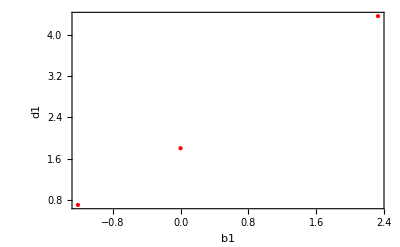

```mathematica
ListPlot[{{-1.21,0.70},{0,1.8},{2.33,-1.92+2π}},PlotStyle->{PointSize[Large],Red},Frame->True,FrameLabel->{"b1","d1","38ns",""}]
```

```mathematica
manipul[Sequence@@sol[[-1,1]]]
```

```mathematica
(Print[#];myMinimize[{
{#,{0,b1,0,b2,0,0.13,-0.39,-0.13,-0.41,0.025,0.045,0.019,0,d1,0,d2}}
}][[2]])&/@{2,8,14,20,26,32,38,44,48}
```

2

8

14

20

26

32

38

44

48

```mathematica
%6268
```

{{b1→0.824933,b2→1.43555,d1→2.16949,d2→0.270038},{b1→-1.63513,b2→0.131985,d1→-0.328666,d2→-0.714283},{b1→-0.922446,b2→0.973729,d1→0.311034,d2→-0.0889069},{b1→-0.874907,b2→1.00103,d1→0.189676,d2→-0.153896},{b1→0.787967,b2→2.16761,d1→2.30741,d2→1.39468},{b1→-2.66579,b2→0.184908,d1→-1.32035,d2→-0.770236},{b1→-1.95327,b2→1.15933,d1→0.0452434,d2→0.935177},{b1→0.124108,b2→1.79621,d1→1.90059,d2→1.53089},{b1→-2.09392,b2→0.434226,d1→-0.0348687,d2→0.689061}}

utiliser le 2 ns pour comprendre les éléments 24 et 42, puis le  le 38 ns pour les 13 et 31, puis les 2ns et 14 ns pour les 12 et 21
 le 2 ns vérouille ϵhπx1Tomo -> -0.39 et ϵhπy1Tomo -> -0.41
 le 38 ns vérouille ϵπx2Prep -> 0.13 et la relation d1(b1) @ 38 ns
 les 2ns et 14 ns vérouillent ϵhπx2Tomo → -0.13, ϵhπy2Tomo →+0.025 (compromis 14 ns et 2 ns)
 Peut-on ensuite déterminer θy1 et θy2 ? en refittant le 2ns,14ns, et 38 ns, en laissant tous les angles libres ? 
 C'est peu sensible, mais significatif: On trouve θy1 → 0.045, θy2 → 0.019
 Maintenant qu'on a toutes les ereurs de tomo, on les affine par un FindMinimum en laissant tous les angles libres, de 2 ns à 48 ns par pas de 6 ns

```mathematica
ini1=#[[2]]&/@(%6268//Flatten);
myTimes={2,8,14,20,26,32,38,44,48};
f[i_]:=error[i,paramsAll/.{a1->0,a2->0,c1->0,c2->0,b1->b1[i],b2->b2[i],d1->d1[i],d2->d2[i]}]
Plus@@f/@myTimes
vars1={b1[#]&/@myTimes,b2[#]&/@myTimes,d1[#]&/@myTimes,d2[#]&/@myTimes}//Transpose//Flatten;
ini=Join[Transpose[{vars1,ini1}],Transpose[{{ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2},{0.13,-0.39,-0.13,-0.41,.025,.045,.019}}]]
NMinimize[]
```

error[2,{0,b1[2],0,b2[2],ϵ,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,d1[2],0,d2[2]}]+error[8,{0,b1[8],0,b2[8],ϵ,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,d1[8],0,d2[8]}]+error[14,{0,b1[14],0,b2[14],ϵ,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,d1[14],0,d2[14]}]+error[20,{0,b1[20],0,b2[20],ϵ,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,d1[20],0,d2[20]}]+error[26,{0,b1[26],0,b2[26],ϵ,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,d1[26],0,d2[26]}]+error[32,{0,b1[32],0,b2[32],ϵ,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,d1[32],0,d2[32]}]+error[38,{0,b1[38],0,b2[38],ϵ,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,d1[38],0,d2[38]}]+error[44,{0,b1[44],0,b2[44],ϵ,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,d1[44],0,d2[44]}]+error[48,{0,b1[48],0,b2[48],ϵ,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,d1[48],0,d2[48]}]

{{b1[2],0.824933},{b2[2],1.43555},{d1[2],2.16949},{d2[2],0.270038},{b1[8],-1.63513},{b2[8],0.131985},{d1[8],-0.328666},{d2[8],-0.714283},{b1[14],-0.922446},{b2[14],0.973729},{d1[14],0.311034},{d2[14],-0.0889069},{b1[20],-0.874907},{b2[20],1.00103},{d1[20],0.189676},{d2[20],-0.153896},{b1[26],0.787967},{b2[26],2.16761},{d1[26],2.30741},{d2[26],1.39468},{b1[32],-2.66579},{b2[32],0.184908},{d1[32],-1.32035},{d2[32],-0.770236},{b1[38],-1.95327},{b2[38],1.15933},{d1[38],0.0452434},{d2[38],0.935177},{b1[44],0.124108},{b2[44],1.79621},{d1[44],1.90059},{d2[44],1.53089},{b1[48],-2.09392},{b2[48],0.434226},{d1[48],-0.0348687},{d2[48],0.689061},{ϵπx2Prep,0.13},{ϵhπx1Tomo,-0.39},{ϵhπx2Tomo,-0.13},{ϵhπy1Tomo,-0.41},{ϵhπy2Tomo,0.025},{θy1,0.045},{θy2,0.019}}

```mathematica
myMinimize[list_?ListQ,mode_:"NMinimize"]:=
Block[{list2=Take[#,2]&/@list,paramsAll2,vars,s},
paramsAll2=#[[-1]]&/@list2;
vars=Select[Union@@paramsAll2,Not[NumberQ[#]]&];
s=If[mode!="NMinimize",FindMinimum[error[list2],Transpose[{vars,ConstantArray[0,Length[vars]]}]],NMinimize[error[list2],vars]];Append[s,list/.s[[-1]]]]
```

```mathematica
Take[#,2]&/@{
{2,{0,b11,0,b21,0,0.13,-0.39,-0.13,-0.41,0.025,θy1,θy2,0,d11,0,d21}},{14,{0,b12,0,b22,0,0.13,-0.39,-0.13,-0.41,.025,θy1,θy2,0,d12,0,d22}},
{38,{0,b13,0,b23,0,0.13,-0.39,-0.13,-0.41,.025,θy1,θy2,0,d13,0,d23}}
}
```

```mathematica
sol[[2]]
```

{b12→-0.46832,b13→-0.606083,b22→0.804535,b23→-0.264204,d12→0.761953,d13→1.38747,d22→-0.254038,d23→-0.486322,θy1→0.0517684,θy2→0.0116346}

```mathematica
Clear[d21]
```

```mathematica
sol=myMinimize[{
{2,{0,b11,0,b21,0,0.13,-0.39,-0.13,-0.41,0.025,θy1,θy2,0,d11,0,d21}},{14,{0,b12,0,b22,0,0.13,-0.39,-0.13,-0.41,.025,θy1,θy2,0,d12,0,d22}},
{38,{0,b13,0,b23,0,0.13,-0.39,-0.13,-0.41,.025,θy1,θy2,0,d13,0,d23}}
}];
plotAtTime[sol[[-1]]]
sol[[2]]
```

-Graphics-

{b11→-0.943792,b12→-0.257924,b13→0.154613,b21→0.542945,b22→1.21063,b23→-0.307098,d11→0.400513,d12→0.975465,d13→2.15313,d21→-0.622683,d22→0.148104,d23→-0.53105,θy1→0.0449477,θy2→0.0185538}

```mathematica
sol=myMinimize[{
{2,{0,b11,0,b21,0,0.13,-0.39,ϵhπx2Tomo,-0.41,ϵhπy2Tomo,θy1,θy2,0,d11,0,d21}},{14,{0,b12,0,b22,0,0.13,-0.39,ϵhπx2Tomo,-0.41,ϵhπy2Tomo,θy1,θy2,0,d12,0,d22}}
}];
plotAtTime[sol[[-1]]]
sol[[2]]
```

-Graphics-

{b12→-1.05873,b22→0.281011,d12→0.182272,d22→-0.793897,ϵhπx2Tomo→-0.129731,ϵhπy2Tomo→0.0250286,θy1→0.0224597,θy2→0.0355704}

```mathematica
sol=myMinimize[{
{14,{0,b1,0,b2,0,0.13,-0.39,ϵhπx2Tomo,-0.41,ϵhπy2Tomo,θy1,θy2,0,d1,0,d2}}
}];
plotAtTime[sol[[-1]]]
sol[[2]]
```

-Graphics-

{b1→-1.09644,b2→-1.01831,d1→0.489289,d2→-1.75833,ϵhπx2Tomo→-0.137805,ϵhπy2Tomo→-0.0753906,θy1→0.0197251,θy2→-0.00726596}

```mathematica
sol=myMinimize[{
{2,{0,b11,0,b21,0,0.13,-0.39,ϵhπx2Tomo,-0.41,ϵhπy2Tomo,θy1,θy2,0,d11,0,d21}},{38,{0,b12,0,b22,0,0.13,-0.39,ϵhπx2Tomo,-0.41,ϵhπy2Tomo,θy1,θy2,0,d12,0,d22}}
}];
plotAtTime[sol[[-1]]]
sol[[2]]
```

```mathematica
sol=myMinimize[{
{38,{0,b1,0,b2,0,ϵπx2Prep,-0.39,ϵhπx2Tomo,-0.41,ϵhπy2Tomo,θy1,θy2,0,d1,0,d2}}
}];
plotAtTime[sol[[-1]]]
sol[[2]]
```

-Graphics-

{b1→-1.21064,b2→-0.74205,d1→0.701971,d2→-0.994577,ϵhπx2Tomo→-0.0528494,ϵhπy2Tomo→0.0274287,ϵπx2Prep→0.130362,θy1→0.129206,θy2→-0.017118}

```mathematica
sol=myMinimize[{
{2,{0,b1,0,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,d1,0,d2}}
}];
plotAtTime[sol[[-1]]]
sol[[2]]
```

-Graphics-

{b1→-1.17157,b2→1.57538,d1→-1.96763,d2→-1.70452,ϵhπx1Tomo→-0.393739,ϵhπx2Tomo→-0.211289,ϵhπy1Tomo→-0.40848,ϵhπy2Tomo→-0.0387448,ϵπx2Prep→-0.11217,θy1→-0.0889259,θy2→0.0438403}

```mathematica
myMinimize[2,{a1,0,a2,0,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,0,c2,0},"FindMinimum"]
```

{0.00535685,{a1→-0.586387,a2→0.0345761,ϵπx2Prep→0.112169,ϵhπx1Tomo→-0.393739,ϵhπx2Tomo→-0.211288,ϵhπy1Tomo→-0.40848,ϵhπy2Tomo→-0.0387449,θy1→-0.088926,θy2→0.0438406,c1→0.586384,c2→-0.0345802},{-0.586387,0,0.0345761,0,0,0.112169,-0.393739,-0.211288,-0.40848,-0.0387449,-0.088926,0.0438406,0.586384,0,-0.0345802,0}}

```mathematica
sol=myMinimize[{
{4,{0,b1,0,b2,0,ϵπx2Prep,ϵhπx1Tomo,0,ϵhπy1Tomo,0,0,0,0,0,0,0}}
}];
plotAtTime[sol[[-1]]]
sol[[2]]
```

-Graphics-

{b1→-2.76622,b2→-0.563817,ϵhπx1Tomo→-0.41531,ϵhπy1Tomo→-0.436423,ϵπx2Prep→-0.103188}

```mathematica
sol
```

{0.00687885,{b1→-2.90194,b2→-0.478965,ϵhπx1Tomo→-0.393431,ϵhπy1Tomo→-0.408424,ϵπx2Prep→-0.106556},{{2,{0,-2.90194,0,-0.478965,0,-0.106556,-0.393431,0,-0.408424,0,0,0,0,0,0,0}}}}

```mathematica
manipul[Sequence@@sol[[-1,1]]]
```

```mathematica
solu[[2]]
```

{a1→0.0530703,a2→0.35292,b1→-0.48179,b2→0.707825,c1→0.0540502,c2→0.352142,d1→0.639699,d2→-0.465383,ϵhπx1Tomo→-0.391762,ϵhπx2Tomo→-0.0726805,ϵhπy1Tomo→-0.454537,ϵhπy2Tomo→0.0234087,ϵπx2Prep→0.12556,θy1→0.0383164,θy2→0.0586448}

```mathematica
sol=myMinimize[{
{0,{0,b1,0,b2,0,0.12,-0.39,ϵhπx2Tomo,-0.42,0,0,0,0,0,0,0}}
}];
plotAtTime[sol[[-1]]]
sol
```

-Graphics-

{0.608903,{b1→4.28931,b2→0.871042,ϵhπx2Tomo→-0.122186},{{0,{0,4.28931,0,0.871042,0,0.12,-0.39,-0.122186,-0.42,0,0,0,0,0,0,0}}}}

```mathematica
sol=myMinimize[{
{2,{0,b1,0,b2,0,0.12,-0.39,ϵhπx2Tomo,-0.42,0,0,0,0,0,0,0}}
}];
plotAtTime[sol[[-1]]]
sol
```

-Graphics-

{0.00569838,{b1→-1.99806,b2→0.423411,ϵhπx2Tomo→-0.208687},{{2,{0,-1.99806,0,0.423411,0,0.12,-0.39,-0.208687,-0.42,0,0,0,0,0,0,0}}}}

```mathematica
manipul[Sequence@@sol[[-1,1]]]
```

```mathematica
sol=myMinimize[{
{2,{a1,b1,a,b2,0,0.12,-0.39,ϵhπx2Tomo,-0.42,0,0,0,0,0,0,0}},
{30,{0,b1,0,b2,0,.12,-0.39,ϵhπx2Tomo,-0.42,0,0,0,0,0,0,0}}
}];
```

```mathematica
solu[[2]]
```

{a1→0.0530703,a2→0.35292,b1→-0.48179,b2→0.707825,c1→0.0540502,c2→0.352142,d1→0.639699,d2→-0.465383,ϵhπx1Tomo→-0.391762,ϵhπx2Tomo→-0.0726805,ϵhπy1Tomo→-0.454537,ϵhπy2Tomo→0.0234087,ϵπx2Prep→0.12556,θy1→0.0383164,θy2→0.0586448}

```mathematica
sol=myMinimize[{
{2,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,0,0,0}},
{10,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,0,0,0}},
{18,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,0,0,0}},
{26,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,0,0,0}},
{34,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,0,0,0}},
{40,{a1,b1,a2,b2,ϵ40,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,0,0,0}},
{48,{a1,b1,a2,b2,ϵ48,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,0,0,0}}
}];
```

-Graphics-

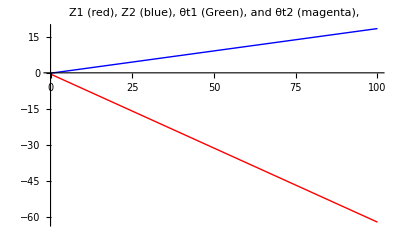

{0.516662,{a1→-0.617273,a2→0.18619,b1→-0.518641,b2→-0.166668,ϵ40→-0.47556,ϵ48→-0.147191,ϵhπx1Tomo→-0.453366,ϵhπx2Tomo→-0.0169366,ϵhπy1Tomo→-0.458436,ϵhπy2Tomo→-0.0484263,ϵπx2Prep→-0.053364,θy1→0.0274518,θy2→0.0319381},{{2,{-0.617273,-0.518641,0.18619,-0.166668,0,-0.053364,-0.453366,-0.0169366,-0.458436,-0.0484263,0.0274518,0.0319381,0,0,0,0}},{10,{-0.617273,-0.518641,0.18619,-0.166668,0,-0.053364,-0.453366,-0.0169366,-0.458436,-0.0484263,0.0274518,0.0319381,0,0,0,0}},{18,{-0.617273,-0.518641,0.18619,-0.166668,0,-0.053364,-0.453366,-0.0169366,-0.458436,-0.0484263,0.0274518,0.0319381,0,0,0,0}},{26,{-0.617273,-0.518641,0.18619,-0.166668,0,-0.053364,-0.453366,-0.0169366,-0.458436,-0.0484263,0.0274518,0.0319381,0,0,0,0}},{34,{-0.617273,-0.518641,0.18619,-0.166668,0,-0.053364,-0.453366,-0.0169366,-0.458436,-0.0484263,0.0274518,0.0319381,0,0,0,0}},{40,{-0.617273,-0.518641,0.18619,-0.166668,-0.47556,-0.053364,-0.453366,-0.0169366,-0.458436,-0.0484263,0.0274518,0.0319381,0,0,0,0}},{48,{-0.617273,-0.518641,0.18619,-0.166668,-0.147191,-0.053364,-0.453366,-0.0169366,-0.458436,-0.0484263,0.0274518,0.0319381,0,0,0,0}}}}

```mathematica
plotAtTime[sol[[-1]]]

Plot[{(a1 t+b1 )/.sol[[2]],(a2 t+b2 )/.sol[[2]],(c1 t+d1 )/.sol[[2]],(c2 t+d2 )/.sol[[2]]},{t,0,100},PlotStyle->{Red,Blue,RGBColor[0,0.5,0],Magenta},PlotLabel->"Z1 (red), Z2 (blue), θt1 (Green), and θt2 (magenta),"]

sol0c=sol
```

```mathematica
{f1,f2}={a1,a2}/2/π 1000/.sol[[2]]//Round
```

{-98,30}

```mathematica
sol=myMinimize[{
{2,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,0,0,0}},
{6,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,0,0,0}},
{10,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,0,0,0}},
{14,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,0,0,0}},
{18,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,0,0,0}},{22,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,0,0,0}},
{26,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,0,0,0}},
{30,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,0,0,0}},
{34,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,0,0,0,0}}}];
```

-Graphics-

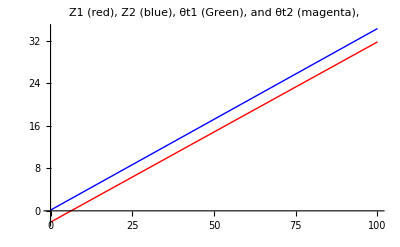

{0.375609,{a1→0.339462,a2→0.341952,b1→-2.12732,b2→0.136836,ϵhπx1Tomo→-0.410861,ϵhπx2Tomo→-0.0286357,ϵhπy1Tomo→-0.443301,ϵhπy2Tomo→-0.0874973,ϵπx2Prep→-0.0255361,θy1→0.0285464,θy2→0.0248022},{{2,{0.339462,-2.12732,0.341952,0.136836,0,-0.0255361,-0.410861,-0.0286357,-0.443301,-0.0874973,0.0285464,0.0248022,0,0,0,0}},{6,{0.339462,-2.12732,0.341952,0.136836,0,-0.0255361,-0.410861,-0.0286357,-0.443301,-0.0874973,0.0285464,0.0248022,0,0,0,0}},{10,{0.339462,-2.12732,0.341952,0.136836,0,-0.0255361,-0.410861,-0.0286357,-0.443301,-0.0874973,0.0285464,0.0248022,0,0,0,0}},{14,{0.339462,-2.12732,0.341952,0.136836,0,-0.0255361,-0.410861,-0.0286357,-0.443301,-0.0874973,0.0285464,0.0248022,0,0,0,0}},{18,{0.339462,-2.12732,0.341952,0.136836,0,-0.0255361,-0.410861,-0.0286357,-0.443301,-0.0874973,0.0285464,0.0248022,0,0,0,0}},{22,{0.339462,-2.12732,0.341952,0.136836,0,-0.0255361,-0.410861,-0.0286357,-0.443301,-0.0874973,0.0285464,0.0248022,0,0,0,0}},{26,{0.339462,-2.12732,0.341952,0.136836,0,-0.0255361,-0.410861,-0.0286357,-0.443301,-0.0874973,0.0285464,0.0248022,0,0,0,0}},{30,{0.339462,-2.12732,0.341952,0.136836,0,-0.0255361,-0.410861,-0.0286357,-0.443301,-0.0874973,0.0285464,0.0248022,0,0,0,0}},{34,{0.339462,-2.12732,0.341952,0.136836,0,-0.0255361,-0.410861,-0.0286357,-0.443301,-0.0874973,0.0285464,0.0248022,0,0,0,0}}}}

```mathematica
plotAtTime[sol[[-1]]]

Plot[{(a1 t+b1 )/.sol[[2]],(a2 t+b2 )/.sol[[2]],(c1 t+d1 )/.sol[[2]],(c2 t+d2 )/.sol[[2]]},{t,0,100},PlotStyle->{Red,Blue,RGBColor[0,0.5,0],Magenta},PlotLabel->"Z1 (red), Z2 (blue), θt1 (Green), and θt2 (magenta),"]

sol0b=sol
```

```mathematica
{f1,f2}={a1,a2}/2/π 1000/.sol0b[[2]]//Round
```

{54,54}

```mathematica
sol=myMinimize[{
{2,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}},
{16,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}},
{30,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}},
{44,{a1,b1,a2,b2,0.1,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}},
{60,{a1,b1,a2,b2,0.3,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}},
{76,{a1,b1,a2,b2,0.40,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}},
{90,{a1,b1,a2,b2,0.45,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}}
}];
```

-Graphics-

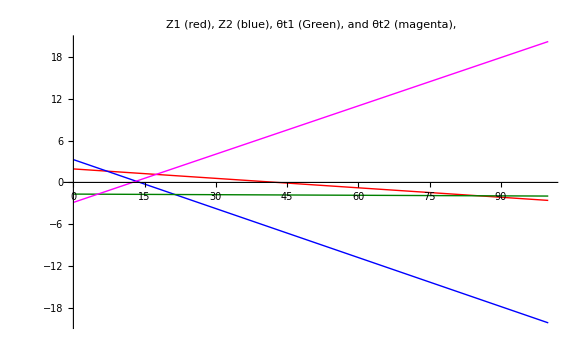

{0.644603,{a1→-0.0451707,a2→-0.234202,b1→1.93742,b2→3.27274,c1→-0.0028325,c2→0.230824,d1→-1.67307,d2→-2.86776,ϵhπx1Tomo→-0.408867,ϵhπx2Tomo→-0.0293711,ϵhπy1Tomo→-0.435758,ϵhπy2Tomo→0.00930514,ϵπx2Prep→-0.110512,θy1→0.0236335,θy2→0.0222347},{{2,{-0.0451707,1.93742,-0.234202,3.27274,0,-0.110512,-0.408867,-0.0293711,-0.435758,0.00930514,0.0236335,0.0222347,-0.0028325,-1.67307,0.230824,-2.86776}},{16,{-0.0451707,1.93742,-0.234202,3.27274,0,-0.110512,-0.408867,-0.0293711,-0.435758,0.00930514,0.0236335,0.0222347,-0.0028325,-1.67307,0.230824,-2.86776}},{30,{-0.0451707,1.93742,-0.234202,3.27274,0,-0.110512,-0.408867,-0.0293711,-0.435758,0.00930514,0.0236335,0.0222347,-0.0028325,-1.67307,0.230824,-2.86776}},{44,{-0.0451707,1.93742,-0.234202,3.27274,0.1,-0.110512,-0.408867,-0.0293711,-0.435758,0.00930514,0.0236335,0.0222347,-0.0028325,-1.67307,0.230824,-2.86776}},{60,{-0.0451707,1.93742,-0.234202,3.27274,0.3,-0.110512,-0.408867,-0.0293711,-0.435758,0.00930514,0.0236335,0.0222347,-0.0028325,-1.67307,0.230824,-2.86776}},{76,{-0.0451707,1.93742,-0.234202,3.27274,0.4,-0.110512,-0.408867,-0.0293711,-0.435758,0.00930514,0.0236335,0.0222347,-0.0028325,-1.67307,0.230824,-2.86776}},{90,{-0.0451707,1.93742,-0.234202,3.27274,0.45,-0.110512,-0.408867,-0.0293711,-0.435758,0.00930514,0.0236335,0.0222347,-0.0028325,-1.67307,0.230824,-2.86776}}}}

```mathematica
plotAtTime[sol[[-1]]]

Plot[{(a1 t+b1 )/.sol[[2]],(a2 t+b2 )/.sol[[2]],(c1 t+d1 )/.sol[[2]],(c2 t+d2 )/.sol[[2]]},{t,0,100},PlotStyle->{Red,Blue,RGBColor[0,0.5,0],Magenta},PlotLabel->"Z1 (red), Z2 (blue), θt1 (Green), and θt2 (magenta),"]

sol0=sol
```

```mathematica
sol=myMinimize[{
{2,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}},
{6,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}},
{10,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}},
{14,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}},
{18,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}},{22,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}},
{26,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}},
{30,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}},
{34,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}}}];
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

-Graphics-

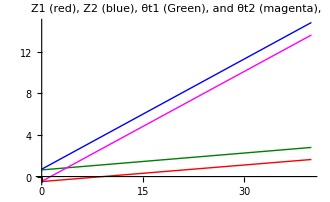

{0.298426,{a1→0.0530703,a2→0.35292,b1→-0.48179,b2→0.707825,c1→0.0540502,c2→0.352142,d1→0.639699,d2→-0.465383,ϵhπx1Tomo→-0.391762,ϵhπx2Tomo→-0.0726805,ϵhπy1Tomo→-0.454537,ϵhπy2Tomo→0.0234087,ϵπx2Prep→0.12556,θy1→0.0383164,θy2→0.0586448},{{2,{0.0530703,-0.48179,0.35292,0.707825,0,0.12556,-0.391762,-0.0726805,-0.454537,0.0234087,0.0383164,0.0586448,0.0540502,0.639699,0.352142,-0.465383}},{6,{0.0530703,-0.48179,0.35292,0.707825,0,0.12556,-0.391762,-0.0726805,-0.454537,0.0234087,0.0383164,0.0586448,0.0540502,0.639699,0.352142,-0.465383}},{10,{0.0530703,-0.48179,0.35292,0.707825,0,0.12556,-0.391762,-0.0726805,-0.454537,0.0234087,0.0383164,0.0586448,0.0540502,0.639699,0.352142,-0.465383}},{14,{0.0530703,-0.48179,0.35292,0.707825,0,0.12556,-0.391762,-0.0726805,-0.454537,0.0234087,0.0383164,0.0586448,0.0540502,0.639699,0.352142,-0.465383}},{18,{0.0530703,-0.48179,0.35292,0.707825,0,0.12556,-0.391762,-0.0726805,-0.454537,0.0234087,0.0383164,0.0586448,0.0540502,0.639699,0.352142,-0.465383}},{22,{0.0530703,-0.48179,0.35292,0.707825,0,0.12556,-0.391762,-0.0726805,-0.454537,0.0234087,0.0383164,0.0586448,0.0540502,0.639699,0.352142,-0.465383}},{26,{0.0530703,-0.48179,0.35292,0.707825,0,0.12556,-0.391762,-0.0726805,-0.454537,0.0234087,0.0383164,0.0586448,0.0540502,0.639699,0.352142,-0.465383}},{30,{0.0530703,-0.48179,0.35292,0.707825,0,0.12556,-0.391762,-0.0726805,-0.454537,0.0234087,0.0383164,0.0586448,0.0540502,0.639699,0.352142,-0.465383}},{34,{0.0530703,-0.48179,0.35292,0.707825,0,0.12556,-0.391762,-0.0726805,-0.454537,0.0234087,0.0383164,0.0586448,0.0540502,0.639699,0.352142,-0.465383}}}}

```mathematica
plotAtTime[sol[[-1]]]

Plot[{(a1 t+b1 )/.sol[[2]],(a2 t+b2 )/.sol[[2]],(c1 t+d1 )/.sol[[2]],(c2 t+d2 )/.sol[[2]]},{t,0,40},PlotStyle->{Red,Blue,RGBColor[0,0.5,0],Magenta},PlotLabel->"Z1 (red), Z2 (blue), θt1 (Green), and θt2 (magenta),"]

sol1=sol
```

La phase Z1 du qubit 1 tourne à 8.4 MHz et la phase Z2 à 56 MHz
De même les référentiels de tomographie tournent à la même vitesse.

```mathematica
{f1,f2,f3,f4}={a1,a2,c1,d1}/2/π 1000/.sol1[[2]]//Round
```

{8,56,9,102}

Notons que le fit a été fait sur des images séparés de 4 ns, ce qui correspond à p= 3% et 22% de tours:

```mathematica
f1.004
f2.004
```

0.032

0.224

Un possible effet stroboscopique conduit à l'une des fréquences suivantes

```mathematica
(1 +Range[-4,4]/(#.004))#&/@{f1,f2,f3,f4}//Round//MatrixForm
```

(-992 | -742 | -492 | -242 | 8 | 258 | 508 | 758 | 1008
-944 | -694 | -444 | -194 | 56 | 306 | 556 | 806 | 1056
-991 | -741 | -491 | -241 | 9 | 259 | 509 | 759 | 1009
-898 | -648 | -398 | -148 | 102 | 352 | 602 | 852 | 1102)

En plottant à 2, 4, et 6 ns on ne voit rien d'anormal.

```mathematica
paramsAll1=sol[[-1,1,2]];
plotAtTime[{{2,paramsAll1},{4,paramsAll1},{6,paramsAll1}}]
```

-Graphics-

Refitons avec 2,14,30 en imposant ou non les a b c d

```mathematica
sol=myMinimize[{
{2,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}},
{14,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}},
{30,{a1,b1,a2,b2,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}}}];
```

-Graphics-

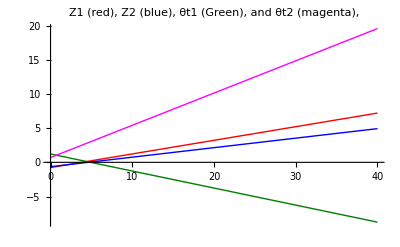

{0.166769,{a1→0.199162,a2→0.139061,b1→-0.763959,b2→-0.637448,c1→-0.249069,c2→0.471417,d1→1.21912,d2→0.699042,ϵhπx1Tomo→-0.402729,ϵhπx2Tomo→-0.102617,ϵhπy1Tomo→-0.445642,ϵhπy2Tomo→-0.114447,ϵπx2Prep→0.0840684,θy1→0.0728302,θy2→-0.00434451},{{2,{0.199162,-0.763959,0.139061,-0.637448,0,0.0840684,-0.402729,-0.102617,-0.445642,-0.114447,0.0728302,-0.00434451,-0.249069,1.21912,0.471417,0.699042}},{14,{0.199162,-0.763959,0.139061,-0.637448,0,0.0840684,-0.402729,-0.102617,-0.445642,-0.114447,0.0728302,-0.00434451,-0.249069,1.21912,0.471417,0.699042}},{30,{0.199162,-0.763959,0.139061,-0.637448,0,0.0840684,-0.402729,-0.102617,-0.445642,-0.114447,0.0728302,-0.00434451,-0.249069,1.21912,0.471417,0.699042}}}}

```mathematica
plotAtTime[sol[[-1]]]

Plot[{(a1 t+b1 )/.sol[[2]],(a2 t+b2 )/.sol[[2]],(c1 t+d1 )/.sol[[2]],(c2 t+d2 )/.sol[[2]]},{t,0,40},PlotStyle->{Red,Blue,RGBColor[0,0.5,0],Magenta},PlotLabel->"Z1 (red), Z2 (blue), θt1 (Green), and θt2 (magenta),"]

sol2=sol
```

Le fit est aussi bon  mais les fréquences sont complètement différentes

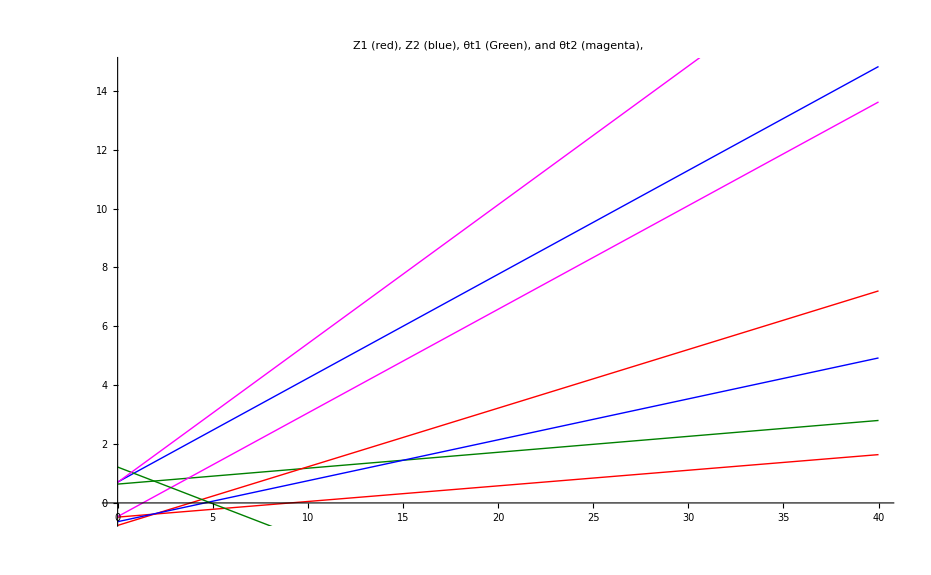

```mathematica
Show[%5507,%5503]
```

```mathematica
{f1,f2,f3,f4}={a1,a2,c1,d1}/2/π 1000/.sol2[[2]]//Round
(1 +Range[-4,4]/(#.004))#&/@{f1,f2,f3,f4}//Round//MatrixForm
```

{32,22,-40,194}

(-968 | -718 | -468 | -218 | 32 | 282 | 532 | 782 | 1032
-978 | -728 | -478 | -228 | 22 | 272 | 522 | 772 | 1022
-1040 | -790 | -540 | -290 | -40 | 210 | 460 | 710 | 960
-806 | -556 | -306 | -56 | 194 | 444 | 694 | 944 | 1194)

à comparer au coup d'avant:

(-992 | -742 | -492 | -242 | 8 | 258 | 508 | 758 | 1008
-944 | -694 | -444 | -194 | 56 | 306 | 556 | 806 | 1056
-991 | -741 | -491 | -241 | 9 | 259 | 509 | 759 | 1009
-898 | -648 | -398 | -148 | 102 | 352 | 602 | 852 | 1102)

imposant les a b c d  de sol1 on retrouve le m^me fit

```mathematica
a11=a1/.sol1[[2]];
b11=b1/.sol1[[2]];
c11=c1/.sol1[[2]];
d11=d1/.sol1[[2]];
a21=a2/.sol1[[2]];
b21=b2/.sol1[[2]];
c21=c2/.sol1[[2]];
d21=d2/.sol1[[2]];
sol=myMinimize[{
{2,{a11,b11,a21,b21,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c11,d11,c21,d21}},
{14,{a11,b11,a21,b21,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c11,d11,c21,d21}},
{30,{a11,b11,a21,b21,0,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c11,d11,c21,d21}}}];
```

```mathematica
plotAtTime[sol[[-1]]]

Plot[{(a1 t+b1 )/.sol[[2]],(a2 t+b2 )/.sol[[2]],(c1 t+d1 )/.sol[[2]],(c2 t+d2 )/.sol[[2]]},{t,0,40},PlotStyle->{Red,Blue,RGBColor[0,0.5,0],Magenta},PlotLabel->"Z1 (red), Z2 (blue), θt1 (Green), and θt2 (magenta),"]

sol3=sol
```

-Graphics-

-Graphics-

{0.0755989,{ϵhπx1Tomo→-0.391773,ϵhπx2Tomo→-0.109869,ϵhπy1Tomo→-0.441838,ϵhπy2Tomo→0.0243299,ϵπx2Prep→0.129979,θy1→0.0820938,θy2→0.0634138},{{2,{0.0530703,-0.48179,0.35292,0.707825,0,0.129979,-0.391773,-0.109869,-0.441838,0.0243299,0.0820938,0.0634138,0.0540502,0.639699,0.352142,-0.465383}},{14,{0.0530703,-0.48179,0.35292,0.707825,0,0.129979,-0.391773,-0.109869,-0.441838,0.0243299,0.0820938,0.0634138,0.0540502,0.639699,0.352142,-0.465383}},{30,{0.0530703,-0.48179,0.35292,0.707825,0,0.129979,-0.391773,-0.109869,-0.441838,0.0243299,0.0820938,0.0634138,0.0540502,0.639699,0.352142,-0.465383}}}}

essayons de comprendre

```mathematica
Take[sol1,2]
Take[sol2,2]
```

{0.298426,{a1→0.0530703,a2→0.35292,b1→-0.48179,b2→0.707825,c1→0.0540502,c2→0.352142,d1→0.639699,d2→-0.465383,ϵhπx1Tomo→-0.391762,ϵhπx2Tomo→-0.0726805,ϵhπy1Tomo→-0.454537,ϵhπy2Tomo→0.0234087,ϵπx2Prep→0.12556,θy1→0.0383164,θy2→0.0586448}}

{0.166769,{a1→0.199162,a2→0.139061,b1→-0.763959,b2→-0.637448,c1→-0.249069,c2→0.471417,d1→1.21912,d2→0.699042,ϵhπx1Tomo→-0.402729,ϵhπx2Tomo→-0.102617,ϵhπy1Tomo→-0.445642,ϵhπy2Tomo→-0.114447,ϵπx2Prep→0.0840684,θy1→0.0728302,θy2→-0.00434451}}

```mathematica
manipul[Sequence@@sol3[[-1,3]]]
```

#### Solution

we define the function pauliSetError1 which gives the apparent PauliSet due to tomographic errors for any arbitrary matrix ρMi

```mathematica
params
paramsB
paramsAll
```

{ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,θt1,θt2}

{ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}

{a1,b1,a2,b2,ϵ,ϵπx2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,c1,d1,c2,d2}

```mathematica
solu=sol1
```

{0.298426,{a1→0.0530703,a2→0.35292,b1→-0.48179,b2→0.707825,c1→0.0540502,c2→0.352142,d1→0.639699,d2→-0.465383,ϵhπx1Tomo→-0.391762,ϵhπx2Tomo→-0.0726805,ϵhπy1Tomo→-0.454537,ϵhπy2Tomo→0.0234087,ϵπx2Prep→0.12556,θy1→0.0383164,θy2→0.0586448},{{2,{0.0530703,-0.48179,0.35292,0.707825,0,0.12556,-0.391762,-0.0726805,-0.454537,0.0234087,0.0383164,0.0586448,0.0540502,0.639699,0.352142,-0.465383}},{6,{0.0530703,-0.48179,0.35292,0.707825,0,0.12556,-0.391762,-0.0726805,-0.454537,0.0234087,0.0383164,0.0586448,0.0540502,0.639699,0.352142,-0.465383}},{10,{0.0530703,-0.48179,0.35292,0.707825,0,0.12556,-0.391762,-0.0726805,-0.454537,0.0234087,0.0383164,0.0586448,0.0540502,0.639699,0.352142,-0.465383}},{14,{0.0530703,-0.48179,0.35292,0.707825,0,0.12556,-0.391762,-0.0726805,-0.454537,0.0234087,0.0383164,0.0586448,0.0540502,0.639699,0.352142,-0.465383}},{18,{0.0530703,-0.48179,0.35292,0.707825,0,0.12556,-0.391762,-0.0726805,-0.454537,0.0234087,0.0383164,0.0586448,0.0540502,0.639699,0.352142,-0.465383}},{22,{0.0530703,-0.48179,0.35292,0.707825,0,0.12556,-0.391762,-0.0726805,-0.454537,0.0234087,0.0383164,0.0586448,0.0540502,0.639699,0.352142,-0.465383}},{26,{0.0530703,-0.48179,0.35292,0.707825,0,0.12556,-0.391762,-0.0726805,-0.454537,0.0234087,0.0383164,0.0586448,0.0540502,0.639699,0.352142,-0.465383}},{30,{0.0530703,-0.48179,0.35292,0.707825,0,0.12556,-0.391762,-0.0726805,-0.454537,0.0234087,0.0383164,0.0586448,0.0540502,0.639699,0.352142,-0.465383}},{34,{0.0530703,-0.48179,0.35292,0.707825,0,0.12556,-0.391762,-0.0726805,-0.454537,0.0234087,0.0383164,0.0586448,0.0540502,0.639699,0.352142,-0.465383}}}}

```mathematica
solu={0.29842599002943404,{a1->0.053070346515152717,a2->0.3529196809551023,b1->-0.4817895030983616,b2->0.7078253982408428,c1->0.054050177040714124,c2->0.352142328017367,d1->0.6396985483921418,d2->-0.46538252728810736,ϵhπx1Tomo->-0.3917616735446513,ϵhπx2Tomo->-0.07268045620297146,ϵhπy1Tomo->-0.454537398117848,ϵhπy2Tomo->0.023408660164240657,ϵπx2Prep->0.12556021992127242,θy1->0.038316374272712526,θy2->0.05864478124211527},{{2,{0.053070346515152717,-0.4817895030983616,0.3529196809551023,0.7078253982408428,0,0.12556021992127242,-0.3917616735446513,-0.07268045620297146,-0.454537398117848,0.023408660164240657,0.038316374272712526,0.05864478124211527,0.054050177040714124,0.6396985483921418,0.352142328017367,-0.46538252728810736}},{6,{0.053070346515152717,-0.4817895030983616,0.3529196809551023,0.7078253982408428,0,0.12556021992127242,-0.3917616735446513,-0.07268045620297146,-0.454537398117848,0.023408660164240657,0.038316374272712526,0.05864478124211527,0.054050177040714124,0.6396985483921418,0.352142328017367,-0.46538252728810736}},{10,{0.053070346515152717,-0.4817895030983616,0.3529196809551023,0.7078253982408428,0,0.12556021992127242,-0.3917616735446513,-0.07268045620297146,-0.454537398117848,0.023408660164240657,0.038316374272712526,0.05864478124211527,0.054050177040714124,0.6396985483921418,0.352142328017367,-0.46538252728810736}},{14,{0.053070346515152717,-0.4817895030983616,0.3529196809551023,0.7078253982408428,0,0.12556021992127242,-0.3917616735446513,-0.07268045620297146,-0.454537398117848,0.023408660164240657,0.038316374272712526,0.05864478124211527,0.054050177040714124,0.6396985483921418,0.352142328017367,-0.46538252728810736}},{18,{0.053070346515152717,-0.4817895030983616,0.3529196809551023,0.7078253982408428,0,0.12556021992127242,-0.3917616735446513,-0.07268045620297146,-0.454537398117848,0.023408660164240657,0.038316374272712526,0.05864478124211527,0.054050177040714124,0.6396985483921418,0.352142328017367,-0.46538252728810736}},{22,{0.053070346515152717,-0.4817895030983616,0.3529196809551023,0.7078253982408428,0,0.12556021992127242,-0.3917616735446513,-0.07268045620297146,-0.454537398117848,0.023408660164240657,0.038316374272712526,0.05864478124211527,0.054050177040714124,0.6396985483921418,0.352142328017367,-0.46538252728810736}},{26,{0.053070346515152717,-0.4817895030983616,0.3529196809551023,0.7078253982408428,0,0.12556021992127242,-0.3917616735446513,-0.07268045620297146,-0.454537398117848,0.023408660164240657,0.038316374272712526,0.05864478124211527,0.054050177040714124,0.6396985483921418,0.352142328017367,-0.46538252728810736}},{30,{0.053070346515152717,-0.4817895030983616,0.3529196809551023,0.7078253982408428,0,0.12556021992127242,-0.3917616735446513,-0.07268045620297146,-0.454537398117848,0.023408660164240657,0.038316374272712526,0.05864478124211527,0.054050177040714124,0.6396985483921418,0.352142328017367,-0.46538252728810736}},{34,{0.053070346515152717,-0.4817895030983616,0.3529196809551023,0.7078253982408428,0,0.12556021992127242,-0.3917616735446513,-0.07268045620297146,-0.454537398117848,0.023408660164240657,0.038316374272712526,0.05864478124211527,0.054050177040714124,0.6396985483921418,0.352142328017367,-0.46538252728810736}}}};
```

```mathematica
paramsAllSolu=solu[[3,1,2]];
ruleSolu0=Join[MapThread[#1->#2&,{paramsAll,paramsAllSolu}],{θt1->0,θt2->0}];
ruleSolu1=Join[MapThread[#1->#2&,{paramsAll,paramsAllSolu}],{θt1->c1 t+d1,θt2->c2 t+d2}];
opE2bSolu0=opE2b//.ruleSolu0;
opE2bSolu1[t_]=opE2b//.ruleSolu1;
```

```mathematica
pauliSetErrorSolu0[ρMi_]:=Tr[ρMi.#]&/@opE2bSolu0
pauliSetErrorSolu1[t_,ρMi_]:=Tr[ρMi.#]&/@opE2bSolu1[t]
```

### Removal of tomographic errors only

We now remove the tomographic errors only, keeping the preparation error.
We do as in subsection "Import Pauli sets ..." but with opE2b1 instead of opBase2A.
As {<Pi>}_TomoError = B.ρ⃗, we get ρ⃗ =B^-1{<Pi>}_TomoError and recalculate the correct ρ's from the experimental Pauli sets.

```mathematica
ρM1={{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}};
(ρV1=Transpose[ρM1]//Flatten)//MatrixForm;
```

```mathematica
(matBSolu0=CoefficientArrays[pauliSetErrorSolu0[ρM1],ρV1]//Normal//#[[2]]&)//MatrixForm//Chop;
(matBSolu0Inv=Inverse[matBSolu0]//Chop)//MatrixForm
ρFromPauliSetTomoErrorSolu0=(Chop[Transpose[Partition[matBSolu0Inv.#,4]]])&
```

(0.25 | 0 | 0 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0 | 0 | 0.25
0 | 0.250499 | -0.0147169+0.250662 ⅈ | 0.006932-0.0182022 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.250499 | -0.0147169+0.250662 ⅈ | 0.006932-0.0182022 ⅈ
0 | 0 | 0 | 0 | 0.278457 | 0 | 0 | 0.278457 | -0.0103694+0.270493 ⅈ | 0 | 0 | -0.0103694+0.270493 ⅈ | -0.118296-0.103279 ⅈ | 0 | 0 | -0.118296-0.103279 ⅈ
0 | 0 | 0 | 0 | 0 | 0.279013 | -0.0163921+0.279194 ⅈ | 0.00772106-0.0202741 ⅈ | 0 | -0.0103901+0.271033 ⅈ | -0.270599-0.0263201 ⅈ | 0.0194067+0.00825522 ⅈ | 0 | -0.118533-0.103485 ⅈ | 0.110516-0.11253 ⅈ | -0.0107997+0.00574929 ⅈ
0 | 0.250499 | -0.0147169-0.250662 ⅈ | 0.006932+0.0182022 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.250499 | -0.0147169-0.250662 ⅈ | 0.006932+0.0182022 ⅈ
0.25 | 0 | 0 | -0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0 | 0 | -0.25
0 | 0 | 0 | 0 | 0 | 0.279013 | -0.0163921-0.279194 ⅈ | 0.00772106+0.0202741 ⅈ | 0 | -0.0103901+0.271033 ⅈ | 0.27182-0.00552642 ⅈ | -0.0199818+0.00674525 ⅈ | 0 | -0.118533-0.103485 ⅈ | -0.0965885+0.124689 ⅈ | 0.00423948-0.0114767 ⅈ
0 | 0 | 0 | 0 | 0.278457 | 0 | 0 | -0.278457 | -0.0103694+0.270493 ⅈ | 0 | 0 | 0.0103694-0.270493 ⅈ | -0.118296-0.103279 ⅈ | 0 | 0 | 0.118296+0.103279 ⅈ
0 | 0 | 0 | 0 | 0.278457 | 0 | 0 | 0.278457 | -0.0103694-0.270493 ⅈ | 0 | 0 | -0.0103694-0.270493 ⅈ | -0.118296+0.103279 ⅈ | 0 | 0 | -0.118296+0.103279 ⅈ
0 | 0 | 0 | 0 | 0 | 0.279013 | -0.0163921+0.279194 ⅈ | 0.00772106-0.0202741 ⅈ | 0 | -0.0103901-0.271033 ⅈ | 0.27182+0.00552642 ⅈ | -0.0199818-0.00674525 ⅈ | 0 | -0.118533+0.103485 ⅈ | -0.0965885-0.124689 ⅈ | 0.00423948+0.0114767 ⅈ
0.25 | 0 | 0 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.25 | 0 | 0 | -0.25
0 | 0.250499 | -0.0147169+0.250662 ⅈ | 0.006932-0.0182022 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.250499 | 0.0147169-0.250662 ⅈ | -0.006932+0.0182022 ⅈ
0 | 0 | 0 | 0 | 0 | 0.279013 | -0.0163921-0.279194 ⅈ | 0.00772106+0.0202741 ⅈ | 0 | -0.0103901-0.271033 ⅈ | -0.270599+0.0263201 ⅈ | 0.0194067-0.00825522 ⅈ | 0 | -0.118533+0.103485 ⅈ | 0.110516+0.11253 ⅈ | -0.0107997-0.00574929 ⅈ
0 | 0 | 0 | 0 | 0.278457 | 0 | 0 | -0.278457 | -0.0103694-0.270493 ⅈ | 0 | 0 | 0.0103694+0.270493 ⅈ | -0.118296+0.103279 ⅈ | 0 | 0 | 0.118296-0.103279 ⅈ
0 | 0.250499 | -0.0147169-0.250662 ⅈ | 0.006932+0.0182022 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.250499 | 0.0147169+0.250662 ⅈ | -0.006932-0.0182022 ⅈ
0.25 | 0 | 0 | -0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.25 | 0 | 0 | 0.25)

Chop[Transpose[Partition[matBSolu0Inv.#1,4]]]&

```mathematica
(matBSolu1[t_]=CoefficientArrays[pauliSetErrorSolu1[t,ρM1],ρV1]//Normal//#[[2]]&)//MatrixForm//Chop;
matBSolu1Inv[t_?NumberQ]:=Inverse[matBSolu1[t]]//Chop;
matBSolu1Inv[30]//MatrixForm
ρFromPauliSetTomoErrorSolu1[t_]=(Chop[Transpose[Partition[matBSolu1Inv[t].#,4]]])&
```

(0.25 | 0 | 0 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0 | 0 | 0.25
0 | -0.195706-0.156362 ⅈ | 0.167961-0.186647 ⅈ | -0.0167775+0.00989372 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.195706-0.156362 ⅈ | 0.167961-0.186647 ⅈ | -0.0167775+0.00989372 ⅈ
0 | 0 | 0 | 0 | -0.177336+0.214687 ⅈ | 0 | 0 | -0.177336+0.214687 ⅈ | -0.201943-0.180259 ⅈ | 0 | 0 | -0.201943-0.180259 ⅈ | 0.154964-0.0254316 ⅈ | 0 | 0 | 0.154964-0.0254316 ⅈ
0 | 0 | 0 | 0 | 0 | 0.273098-0.0571473 ⅈ | 0.0411399+0.276632 ⅈ | 0.00340484-0.0214257 ⅈ | 0 | 0.0453431+0.267415 ⅈ | -0.270253+0.0296618 ⅈ | 0.0206861+0.00410532 ⅈ | 0 | -0.137215-0.0770134 ⅈ | 0.0851249-0.13278 ⅈ | -0.0093932+0.0078394 ⅈ
0 | -0.195706+0.156362 ⅈ | 0.167961+0.186647 ⅈ | -0.0167775-0.00989372 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.195706+0.156362 ⅈ | 0.167961+0.186647 ⅈ | -0.0167775-0.00989372 ⅈ
0.25 | 0 | 0 | -0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0 | 0 | -0.25
0 | 0 | 0 | 0 | 0 | 0.0045472-0.278976 ⅈ | -0.279424+0.0118397 ⅈ | 0.0203972-0.00738962 ⅈ | 0 | 0.270828+0.0148059 ⅈ | -0.00109572-0.271874 ⅈ | 0.00641871+0.0200891 ⅈ | 0 | -0.105403+0.11683 ⅈ | 0.123099+0.0986078 ⅈ | -0.0114061-0.00442596 ⅈ
0 | 0 | 0 | 0 | -0.177336+0.214687 ⅈ | 0 | 0 | 0.177336-0.214687 ⅈ | -0.201943-0.180259 ⅈ | 0 | 0 | 0.201943+0.180259 ⅈ | 0.154964-0.0254316 ⅈ | 0 | 0 | -0.154964+0.0254316 ⅈ
0 | 0 | 0 | 0 | -0.177336-0.214687 ⅈ | 0 | 0 | -0.177336-0.214687 ⅈ | -0.201943+0.180259 ⅈ | 0 | 0 | -0.201943+0.180259 ⅈ | 0.154964+0.0254316 ⅈ | 0 | 0 | 0.154964+0.0254316 ⅈ
0 | 0 | 0 | 0 | 0 | 0.0045472+0.278976 ⅈ | -0.279424-0.0118397 ⅈ | 0.0203972+0.00738962 ⅈ | 0 | 0.270828-0.0148059 ⅈ | -0.00109572+0.271874 ⅈ | 0.00641871-0.0200891 ⅈ | 0 | -0.105403-0.11683 ⅈ | 0.123099-0.0986078 ⅈ | -0.0114061+0.00442596 ⅈ
0.25 | 0 | 0 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.25 | 0 | 0 | -0.25
0 | -0.195706-0.156362 ⅈ | 0.167961-0.186647 ⅈ | -0.0167775+0.00989372 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.195706+0.156362 ⅈ | -0.167961+0.186647 ⅈ | 0.0167775-0.00989372 ⅈ
0 | 0 | 0 | 0 | 0 | 0.273098+0.0571473 ⅈ | 0.0411399-0.276632 ⅈ | 0.00340484+0.0214257 ⅈ | 0 | 0.0453431-0.267415 ⅈ | -0.270253-0.0296618 ⅈ | 0.0206861-0.00410532 ⅈ | 0 | -0.137215+0.0770134 ⅈ | 0.0851249+0.13278 ⅈ | -0.0093932-0.0078394 ⅈ
0 | 0 | 0 | 0 | -0.177336-0.214687 ⅈ | 0 | 0 | 0.177336+0.214687 ⅈ | -0.201943+0.180259 ⅈ | 0 | 0 | 0.201943-0.180259 ⅈ | 0.154964+0.0254316 ⅈ | 0 | 0 | -0.154964-0.0254316 ⅈ
0 | -0.195706+0.156362 ⅈ | 0.167961+0.186647 ⅈ | -0.0167775-0.00989372 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.195706-0.156362 ⅈ | -0.167961-0.186647 ⅈ | 0.0167775+0.00989372 ⅈ
0.25 | 0 | 0 | -0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.25 | 0 | 0 | 0.25)

Chop[Transpose[Partition[matBSolu1Inv[t].#1,4]]]&

```mathematica
ρsSolu0=Prepend[ρFromPauliSetTomoErrorSolu0/@Rest[pauliSets],ρs[[1]]];
ρsSolu1=Prepend[MapThread[ρFromPauliSetTomoErrorSolu1[#1][#2]&,{Rest[times],Rest[pauliSets]}],ρs[[1]]];
```

### To physical matrices

Although these ρ's are Hermitian and have a trace 1, they are non physical because they are not positive (all eigenvalues positive)

```mathematica
Min[Chop[Eigenvalues[#]]]&/@ρsSolu0
```

{-0.0295575,-0.0220438,-0.0376107,-0.0490734,-0.0565353,-0.0598504,-0.0778077,-0.0738921,-0.0742717,-0.0696463,-0.0648525,-0.0668774,-0.0575756,-0.0524319,-0.0327921,-0.02093,-0.0331053,-0.0297792,-0.0199819,-0.0263068,-0.0183289,-0.0220675,-0.0199985,-0.0232455,-0.0180997,-0.0226092,-0.0195572,-0.0204415,-0.0205902,-0.0234713,-0.0268873,-0.0194316,-0.029327,-0.035307,-0.0637632,-0.0251283,-0.0279909,-0.0443644,-0.056947,-0.0466414,-0.0424019,-0.0719323,-0.0609821,-0.0512846,-0.0387014,-0.0155296,-0.0120265,-0.00566513,-0.0177558,-0.0304916,-0.0121975,-0.00933354,-0.00304893,-0.00218172,-0.00119053,-0.00417685,-0.00057221,-0.00731487,-0.0106102,-0.00404327,-0.00744725,-0.0097853,-0.015015,-0.0133655,-0.0232437,-0.0190246,-0.0251133,-0.025393,-0.0310275,-0.0165875,-0.0344738,-0.0226637,-0.0313659,-0.022183,-0.020669,-0.0221426,-0.0136226,-0.0117986,-0.0117616,-0.0109357,-0.0121126,-0.0121333,-0.00733697,-0.0108856,-0.00874899,-0.013725,-0.0112943,-0.0133283,-0.0181061,-0.0117707,-0.00561287,-0.0102631,-0.00781881,-0.00663849,-0.00322192,-0.00779644,-0.00186609,-0.00240432,-0.0046909,-0.0045272,-0.00168378,-0.00010885,-0.00181592,0.00281706,-0.00255794,0.000397307,0.0042424,-0.00223655,0.00101444,0.00364125,0.00184767,0.0027633,0.000958395,-0.00266537,-0.00250572,-0.00160769,-0.00519089,-0.0150327,-0.0115764,-0.0117159,-0.00914988,-0.00857682,-0.00724904,-0.00720979,-0.0104772,-0.0136182,-0.0123035,-0.00735665,-0.00908694,-0.00717313,-0.00407141,-0.00271485,-0.00494397,-0.00746784,-0.00512973,-0.00813517,-0.00272869,-0.00483546,-0.00588737,-0.014249,-0.00292797,-0.00628346,-0.0027559,-0.00281375,-0.00434321,-0.00409566,0.000499997,-0.0034772,-0.00407779,-0.00244817,0.00519195,0.00184168,0.00494417,0.0035896,0.000204239,0.0015704,0.00212828,0.000615513,0.00414947,-0.00120189,0.00046838,0.00605756,-0.0016162,0.0042442,0.000879608,0.00196969,-0.00017977,-0.0000234764,0.00192643,-0.00111788,-0.00582267,0.00203247,0.000825828,-0.00378143,-0.000829162,0.00493071,-0.00477125,-0.00531095,-0.00401853,-0.00806439,-0.0010853,-0.00151533,-0.00489607,-0.00447434,-0.00431373,-0.0015478,-0.00495779,-0.0045005,0.000986374,-0.00117565,-0.00467976,-0.00888028,-0.000527485,-0.00297669,-0.00171624,-0.0021369,0.00232335,0.000313136,-0.00153425,-0.0007312,-0.00155959,0.000651576,-0.00214413,0.00138979,-0.00054151,0.00228374,-0.000750507,0.00507115,0.00385577,0.00434951,0.00628768,0.00152574,-0.000593722,0.00465319,0.0101621,0.00125454,-0.000569958,0.00203763,0.00214684,0.000041447,0.00061759,0.00332136,0.00137709,-0.00579849,-0.00163028,0.00113317,0.000247541,-0.00229427,-0.00159673,-0.00281765,-0.000201437,-0.00713,-0.00412855,-0.00108974,-0.00434278,-0.00570048,0.000106894,0.000317869,-0.00346099,0.00457797,-0.00123171,0.0018285,-0.00365386,-0.00111358,0.00240285,0.00180783,-0.00239153,-0.00180473,0.000746172,-0.00044447,5.5679×10^-6,0.00240657,0.000880433,0.0040524,0.00289353,0.0046402,0.0001478,-0.00128501,-0.00225419,0.00393796,0.00383804,0.000727692,0.00490359,0.00605756,-0.0000989081,-0.00157984,-0.000151519,-0.000078007,0.00235474,0.00243216,0.00109703,0.00359071,0.00171877,0.0037036,-0.00194662,0.00113355,-0.000804908,0.00367578,0.00104092,-0.000922073,0.00064699,-0.000549384,-0.00139008,-0.000353129,0.000785135,0.00232457,0.00372476,-0.00215374,-0.00209364,-0.00216131,-0.000814362,0.000606525,-0.00219648,-0.00242313,-0.00295687,-0.00218952,-0.0025655,0.00214079,-0.000415083,0.000802075}

Let us make them physical by minimization of the distance ( Hilbert-Schmitt norm) between each non physical matrices and physical matrices

```mathematica
Remove[d2Num,ρPofρ,ρM2,ρRealL,bestρPofρ]
d2Num[m1_/;And @@ (NumberQ/@Flatten[m1]),m2_/;And @@ (NumberQ/@Flatten[m2])]:=Plus@@(m2-m1//Flatten//Chop//Abs//#^2&)
ρPofρ[ρ_/;And @@ (NumberQ/@Flatten[ρ])]:=Block[{val,vec},
{val,vec}=Eigensystem[ρ]//Chop[#,10^-6]&//Transpose//Sort//Reverse//Transpose;
val=Max[#,0]&/@val;val=val/Plus@@val;
Chop[Transpose[vec].DiagonalMatrix[val].Conjugate[vec],10^-6]
];
ρM2=Table[ρ0[i,j],{i,1,4},{j,1,4}];
ρRealL=MapIndexed[Take[#1,#2[[1]]]&,ρM2,1]//Flatten;
(ρM2=ρM2//.{ρ0[i_,j_]/;j>i->Conjugate[ρ0[j,i]],ρ0[i_,j_]/;j<i->reρ0[i,j]+I imρ0[i,j]}//ComplexExpand)//MatrixForm
ρRealL=ρRealL/.ρ0[i_,j_]/;j≠i->Sequence[reρ0[i,j],imρ0[i,j]]//ComplexExpand
```

(ρ0[1,1] | -ⅈ imρ0[2,1]+reρ0[2,1] | -ⅈ imρ0[3,1]+reρ0[3,1] | -ⅈ imρ0[4,1]+reρ0[4,1]
ⅈ imρ0[2,1]+reρ0[2,1] | ρ0[2,2] | -ⅈ imρ0[3,2]+reρ0[3,2] | -ⅈ imρ0[4,2]+reρ0[4,2]
ⅈ imρ0[3,1]+reρ0[3,1] | ⅈ imρ0[3,2]+reρ0[3,2] | ρ0[3,3] | -ⅈ imρ0[4,3]+reρ0[4,3]
ⅈ imρ0[4,1]+reρ0[4,1] | ⅈ imρ0[4,2]+reρ0[4,2] | ⅈ imρ0[4,3]+reρ0[4,3] | ρ0[4,4])

{ρ0[1,1],reρ0[2,1],imρ0[2,1],ρ0[2,2],reρ0[3,1],imρ0[3,1],reρ0[3,2],imρ0[3,2],ρ0[3,3],reρ0[4,1],imρ0[4,1],reρ0[4,2],imρ0[4,2],reρ0[4,3],imρ0[4,3],ρ0[4,4]}

```mathematica
ρRealLofρ[ρm_]=ρRealL/.{ρ0[i_,j_]->ρm[[i,j]],reρ0[i_,j_]->Re[ρm[[i,j]]],imρ0[i_,j_]->Im[ρm[[i,j]]]}

ρofρRealL[ρReal_]=ρM2/.{
ρ0[i_,j_]:>ρReal[[Flatten[Position[ρRealL,ρ0[i,j]]][[-1]]]],
reρ0[i_,j_]:>ρReal[[Flatten[Position[ρRealL,reρ0[i,j]]][[-1]]]],
imρ0[i_,j_]:>ρReal[[Flatten[Position[ρRealL,imρ0[i,j]]][[-1]]]]}

bestρPofρ[ρm_/;And @@ (NumberQ/@Flatten[ρm]),showProgress_:False]:=Block[{a=If[showProgress,Print["Start minimization"]],sol=FindMinimum[d=d2Num[ρPofρ[ρofρRealL[ρRealL]],ρm],Evaluate[Transpose[{ρRealL,ρRealLofρ[ρm]}]],StepMonitor:>If[showProgress,Print[d],None]]},ρPofρ[ρofρRealL[ρRealL/.sol[[2]]]]]
```

Part::pspec: Part specification i is neither an integer nor a list of integers.

General::stop: Further output of Part will be suppressed during this calculation.

Part::partd: Part specification ρm ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification ρm ⟦ 2, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part will be suppressed during this calculation.

{ρm⟦1,1⟧,Re[ρm⟦2,1⟧],Im[ρm⟦2,1⟧],ρm⟦2,2⟧,Re[ρm⟦3,1⟧],Im[ρm⟦3,1⟧],Re[ρm⟦3,2⟧],Im[ρm⟦3,2⟧],ρm⟦3,3⟧,Re[ρm⟦4,1⟧],Im[ρm⟦4,1⟧],Re[ρm⟦4,2⟧],Im[ρm⟦4,2⟧],Re[ρm⟦4,3⟧],Im[ρm⟦4,3⟧],ρm⟦4,4⟧}

Part::partd: Part specification ρReal ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification ρReal ⟦ 3 ⟧ is longer than depth of object.

Part::partd: Part specification ρReal ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part will be suppressed during this calculation.

{{ρReal⟦1⟧,ρReal⟦2⟧-ⅈ ρReal⟦3⟧,ρReal⟦5⟧-ⅈ ρReal⟦6⟧,ρReal⟦10⟧-ⅈ ρReal⟦11⟧},{ρReal⟦2⟧+ⅈ ρReal⟦3⟧,ρReal⟦4⟧,ρReal⟦7⟧-ⅈ ρReal⟦8⟧,ρReal⟦12⟧-ⅈ ρReal⟦13⟧},{ρReal⟦5⟧+ⅈ ρReal⟦6⟧,ρReal⟦7⟧+ⅈ ρReal⟦8⟧,ρReal⟦9⟧,ρReal⟦14⟧-ⅈ ρReal⟦15⟧},{ρReal⟦10⟧+ⅈ ρReal⟦11⟧,ρReal⟦12⟧+ⅈ ρReal⟦13⟧,ρReal⟦14⟧+ⅈ ρReal⟦15⟧,ρReal⟦16⟧}}

Now the ρ's are physical:

```mathematica
ρsSolu0P=bestρPofρ/@ρsSolu0;
Max[Map[Max[Flatten[Chop[#-ConjugateTranspose[#]]]]&,ρsSolu0P]]
uu=Map[Tr,ρsSolu0P]//Chop;{Min[uu],Max[uu]}
Min[Map[Min[Chop[Eigenvalues[#]]]&,ρsSolu0P]//Chop]
MapThread[d2Num[#1,#2]&,{ρsSolu0P,ρsSolu0}]//Max
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[False].

General::stop: Further output of Flatten will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum will be suppressed during this calculation.

0

{0.999999,1.}

-8.33599×10^-7

0.00907697

```mathematica
ρsSolu1P=bestρPofρ/@ρsSolu1;
Max[Map[Max[Flatten[Chop[#-ConjugateTranspose[#]]]]&,ρsSolu1P]]
uu=Map[Tr,ρsSolu1P]//Chop;{Min[uu],Max[uu]}
Min[Map[Min[Chop[Eigenvalues[#]]]&,ρsSolu1P]//Chop]
MapThread[d2Num[#1,#2]&,{ρsSolu1P,ρsSolu1}]//Max
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[False].

General::stop: Further output of Flatten will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

0

{0.999999,1.}

-8.33592×10^-7

0.00907697

```mathematica
ρGraphSolu1P=myCompareGraph[{#}]&/@ρsSolu1P;
ListAnimate[ρGraphSolu1P]
```

```mathematica
1/22.
```

0.0454545

### Animations

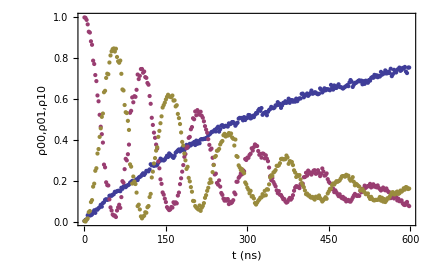

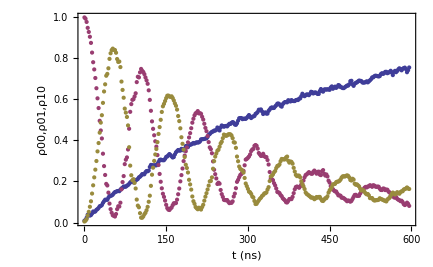

```mathematica
ρ00List=Transpose[{times,#[[1,1]]&/@ρs}];
ρ01List=Transpose[{times,#[[2,2]]&/@ρs}];
ρ10List=Transpose[{times,#[[3,3]]&/@ρs}];
gr0=ListPlot[{ρ00List,ρ01List,ρ10List},Frame->True,FrameLabel->{"t (ns)","ρ00,ρ01,ρ10"}]
ρ00ListS=myMobileAveraging[ρ00List,2];
ρ01ListS=myMobileAveraging[ρ01List,2];
ρ10ListS=myMobileAveraging[ρ10List,2];
gr0b=ListPlot[{ρ00ListS,ρ01ListS,ρ10ListS},Frame->True,FrameLabel->{"t (ns)","ρ00,ρ01,ρ10"}]
```

```mathematica
times[[281]]
```

560.

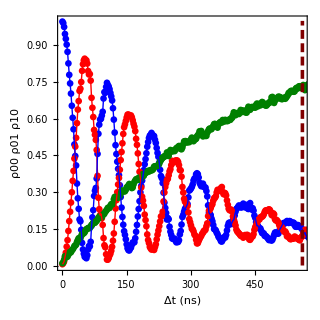

```mathematica
gr0S=ListPlot[{ρ01ListS,ρ10ListS,ρ00ListS},Frame->True,FrameLabel->{"Δt (ns)",Style["ρ01  ",Blue]Style["ρ10  ",Red]Style["ρ00  ",RGBColor[0,0.5,0]]},PlotStyle->{{PointSize->0.015,Blue},{PointSize->0.015,Red},{PointSize->0.015,RGBColor[0,0.5,0]}},BaseStyle->{FontSize->18},AspectRatio->1,ImageSize->320];
gr1=ListPlot[{ρ10ListS,ρ01ListS},Joined->True,PlotStyle->{Red,Blue}];
gr0S=Show[gr0S,gr1,PlotRange->{{0,560},{0,1}}];
gr0St[i_]:=Show[gr0S,Graphics[{RGBColor[0.5,0,0],Thickness[0.008],Dashing[{0.02,0.01}],Line[{{times[[i]],0},{times[[i]],1}}]}],PlotLabel->"  "]
gr0St[281]
```

```mathematica
Options[myPlotElement]
```

{ignoreCell→(False&),offset→{0,0},showFrame→True,frameFaceFunction→({White,Opacity[0]}&),showCentralPoint→False,centralPointSize→Small,show2DShape→True,whatShape→circle,functionFor2DShapeAera→Abs,hide2DShapeSmallerThan→0,borderDirectives→{GrayLevel[0],Thickness[0.001]},fill2DShape→True,fillingColor→(Hue[#2/(2 π)+0.5]&),showArrow→True,functionForArrowLength→Abs,hideArrowSmallerThan→0,arrowDirectives→{GrayLevel[0],Thickness[0.001],Arrowheads[0.05]},showLabel→False,labelFunction→Identity,labelStyle→Small,labelShift→{0,0}}

```mathematica
myTime[i_]:=Style[ " Δt ="<>ToString[PaddedForm[Round[times[[i]]],3]] <> " ns",FontSize->18,RGBColor[0.5,0,0]]
header[i_]:=myTime[i]
xL=-0.35;yL=-3.2;
kets=Graphics[{Text["|00>",{xL,0.5}],Text["|01>",{xL,-0.5}],Text["|10>",{xL,-1.5}],Text["|11>",{xL,-2.5}],Text["<00|",{0.5,yL}],Text["<01|",{1.5,yL}],Text["<10|",{2.5,yL}],Text["<11|",{3.5,yL}]},BaseStyle->{FontSize->18}];
myOpts3={functionForArrowLength->(Sqrt[Abs[#]]&),hideArrowSmallerThan->0.1,fill2DShape->False,borderDirectives->{Red,Thickness[0.005]},arrowDirectives->{Red,Thickness[0.002],Arrowheads[0]}};
myMatrixPlot[ρList_,i_,opts_:myOpts3]:=Block[{label=header[i]},Show[complexMatrixDraw[ρList[[i]],opts],kets,BaseStyle->{FontSize->18},PlotLabel->label,ImageSize->320]];
```

```mathematica
myPlot[ρList_,i_,opts_:myOpts3]:=Graphics[{Inset[myMatrixPlot[ρList,i,opts],{0,0},{4.5,-1},0.95],Inset[gr0St[i],{0,0},{-90,0.5},0.95]},AspectRatio->0.5,ImageSize->800]
```

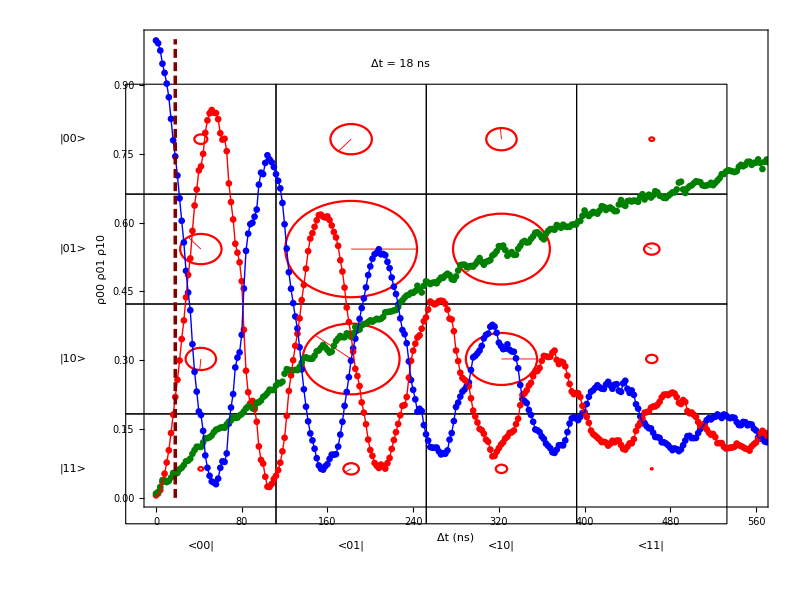

```mathematica
myPlot[ρsSolu0P,10]
```

```mathematica
anim0=myPlot[ρsSolu0P,#]&/@Range[281];
anim1=myPlot[ρsSolu1P,#]&/@Range[281];
```

```mathematica
ListAnimate[anim1]
```

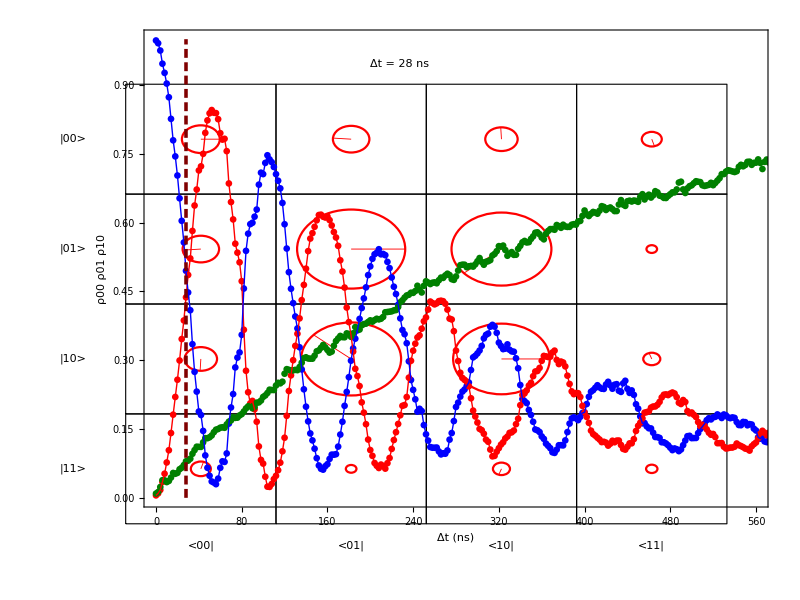

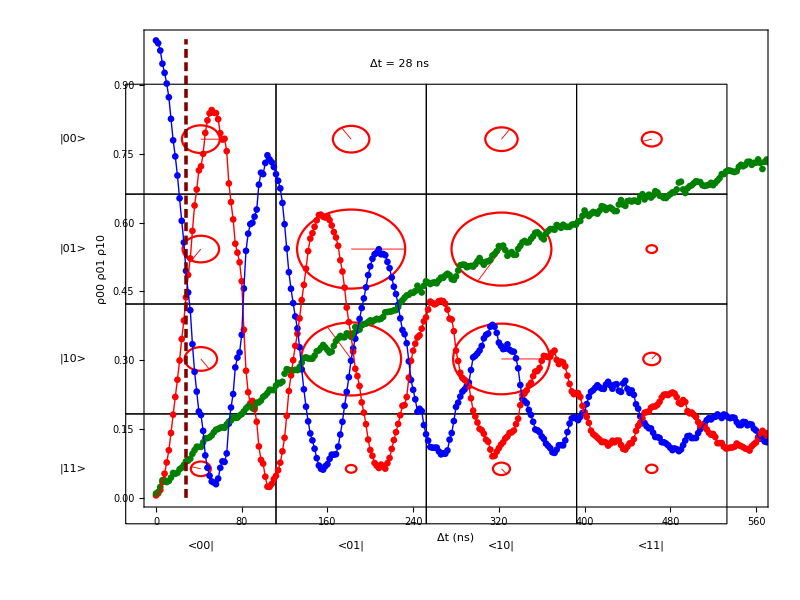

```mathematica
anim0[[15]]
anim1[[15]]
```

```mathematica
Export["U:\\Commun\\PROJET Cavités\\articles\\ISWAP\\material for figures\\Animations\\anim0.gif",anim0,ImageSize->800]
```

```mathematica
Export["U:\\Commun\\PROJET Cavités\\articles\\ISWAP\\material for figures\\Animations\\anim1.gif",anim1,ImageSize->800]
```

U:\Commun\PROJET Cavités\articles\ISWAP\material for figures\Animations\anim1.gif